# Bringing in Data and Quickly Visualizing It

```mathematica
$ImportFormats
```

```mathematica
$ImportFormats//Length
```

We can check what kind of information can be pulled using Import[filenameOrURL, “Elements”] syntax.

```mathematica
SetOptions[SelectedNotebook[],Magnification->1.1]
```

### CSV Example

```mathematica
FileNames["*.csv"]
```

```mathematica
Import["table.csv","Elements"]
```

```mathematica
Import["table.csv","Dimensions"]
```

```mathematica
table=Import["table.csv"]
```

```mathematica
ListPlot[table]
```

```mathematica
ListPlot[table,Joined->True]
```

```mathematica
ListPlot3D[table]
```

```mathematica
ArrayPlot[table]
```

```mathematica
MatrixPlot[table]
```

### XLS Example

```mathematica
FileNames["*.xls"]
```

```mathematica
Import["SampleLabData.xls"]
```

```mathematica
sampleData=Import["SampleLabData.xls"]⟦1⟧
Dimensions[sampleData]
```

```mathematica
ListPlot[sampleData]
```

Fit a model to the data

```mathematica
model=LinearModelFit[sampleData,{1,x,x^2,x^3},x]
```

Visualize the data and the fitted model

```mathematica
Show[ListPlot[sampleData],Plot[model[x],{x,-5,18},PlotStyle->Red]]
```

### HTML Example

```mathematica
SystemOpen["https://gocolumbialions.com/sports/football/roster"]
```

```mathematica
Import["https://gocolumbialions.com/sports/football/roster","Elements"]
```

```mathematica
Import["https://gocolumbialions.com/sports/football/roster","Data"]
```

{{{ Print , 2020_Columbia_Football_Roster.pdf },{ Roster Layout: Go , Choose A Season: 2020 Football Roster 2019 Football Roster 2018 Football Roster 2017 Football Roster 2016 Football Roster 2015 Football Roster 2014 Football Roster 2013 Football Roster 2012 Football Roster 2011 Football Roster 2010 Football Roster 2009 Football Roster 2008 Football Roster 2007 Football Roster 2006 Football Roster 2005 Football Roster Go }},{{{ Defensive Back DB 5'9" 180 lbs CC 2 Will Allen Sr. Pembroke Pines, Fla. American Heritage H.S. Full Bio Senior Pembroke Pines, Fla. American Heritage H.S. Full Bio Hide/Show Additional Information For Will Allen , Quarterback QB 6'1" 215 lbs CC 2 John Foreback Jr. Morristown, Tenn. Morristown West H.S. Full Bio Junior Morristown, Tenn. Morristown West H.S. Full Bio Hide/Show Additional Information For John Foreback , Defensive Back DB 5'11" 185 lbs CC 3 Fara'ad McCombs Jr. Passaic, N.J. St. Joseph Regional Full Bio Junior Passaic, N.J. St. Joseph Regional Full Bio Hide/Show Additional Information For Fara'ad McCombs , Running Back RB 5'9" 225 lbs CC 4 Ryan Young Jr. Wheaton, Ill. Wheaton-Warrenville H.S. Full Bio Junior Wheaton, Ill. Wheaton-Warrenville H.S. Full Bio Hide/Show Additional Information For Ryan Young , Quarterback QB 6'4" 210 lbs CC 5 Joe Green Fr. Sammamish, Wash. Skyline H.S. Full Bio First Year Sammamish, Wash. Skyline H.S. Full Bio Hide/Show Additional Information For Joe Green , Wide Receiver WR 5'11" 180 lbs CC 6 Ernest Robertson Jr. Bronx, N.Y. Riverdale Country School Full Bio Junior Bronx, N.Y. Riverdale Country School Full Bio Hide/Show Additional Information For Ernest Robertson , Defensive Back DB 5'10" 195 lbs CC 7 Ben Mathiasmeier Sr. Katy, Texas Cinco Ranch H.S. Full Bio Senior Katy, Texas Cinco Ranch H.S. Full Bio Hide/Show Additional Information For Ben Mathiasmeier , Running Back RB 5'9" 195 lbs CC 7 Dante Miller Jr. Rockingham, N.C. Richmond Senior H.S. Full Bio Junior Rockingham, N.C. Richmond Senior H.S. Full Bio Hide/Show Additional Information For Dante Miller , Quarterback QB 6'2" 210 lbs CC 8 Dillon Davis Sr. Aledo, Texas Aledo H.S. Full Bio Senior Aledo, Texas Aledo H.S. Full Bio Hide/Show Additional Information For Dillon Davis , Linebacker LB 6'3" 215 lbs CC 8 Scott Valentas So. Wichita, Kansas Kapaun Mount Carmel Catholic H.S. Full Bio Sophomore Wichita, Kansas Kapaun Mount Carmel Catholic H.S. Full Bio Hide/Show Additional Information For Scott Valentas , Quarterback QB 6'2" 220 lbs CC 9 Josh Bean Sr. Hinsdale, Ill. Hinsdale Central H.S. Full Bio Senior Hinsdale, Ill. Hinsdale Central H.S. Full Bio Hide/Show Additional Information For Josh Bean , Defensive Back DB 5'10" 170 lbs CC 9 Bryan Bell-Anderson So. Sarasota, Fla. Dr. Phillips H.S. Full Bio Sophomore Sarasota, Fla. Dr. Phillips H.S. Full Bio Hide/Show Additional Information For Bryan Bell-Anderson , Quarterback QB 6'0" 190 lbs CC 10 Caden Bell So. Placentia, Calif. Junipero Serra Catholic H.S. Full Bio Sophomore Placentia, Calif. Junipero Serra Catholic H.S. Full Bio Hide/Show Additional Information For Caden Bell , Defensive Back DB 6'1" 205 lbs CC 10 Jordan Colbert Jr. Washington, D.C. Gonzaga Prep Full Bio Junior Washington, D.C. Gonzaga Prep Full Bio Hide/Show Additional Information For Jordan Colbert , Wide Receiver WR 5'8" 190 lbs CC 11 Darion Acohido Sr. Henderson, Nevada Liberty H.S. Full Bio Senior Henderson, Nevada Liberty H.S. Full Bio Hide/Show Additional Information For Darion Acohido , Quarterback QB 6'3" 220 lbs CC 12 Ty Lenhart Jr. Gambrills, Md. DeMatha Catholic H.S. Full Bio Junior Gambrills, Md. DeMatha Catholic H.S. Full Bio Hide/Show Additional Information For Ty Lenhart , Linebacker LB 6'2" 205 lbs CC 12 Joshua Smythe-Macaulay Jr. Austin, Texas James Bowie H.S. Full Bio Junior Austin, Texas James Bowie H.S. Full Bio Hide/Show Additional Information For Joshua Smythe-Macaulay , Wide Receiver WR 5'11" 190 lbs CC 13 Josh Wainwright Sr. Austin, Texas James Bowie H.S. Full Bio Senior Austin, Texas James Bowie H.S. Full Bio Hide/Show Additional Information For Josh Wainwright , Linebacker LB 6'0" 205 lbs CC 14 Cameron Brown Jr. Castro Valley, Calif. Castro Valley H.S. Full Bio Junior Castro Valley, Calif. Castro Valley H.S. Full Bio Hide/Show Additional Information For Cameron Brown , Quarterback QB 6'5" 225 lbs CC 14 Kristopher Jenner Fr. Annapolis, Md. McDonogh School Full Bio First Year Annapolis, Md. McDonogh School Full Bio Hide/Show Additional Information For Kristopher Jenner , Linebacker LB 5'11" 225 lbs CC 15 TJ McGarry So. Fort Wayne, Ind. Bishop Dwenger H.S. Full Bio Sophomore Fort Wayne, Ind. Bishop Dwenger H.S. Full Bio Hide/Show Additional Information For TJ McGarry , Quarterback QB 6'3" 210 lbs CC 16 Gabriel Hollingsworth Fr. Pfafftown, N.C. Ronald Reagan H.S. Full Bio First Year Pfafftown, N.C. Ronald Reagan H.S. Full Bio Hide/Show Additional Information For Gabriel Hollingsworth , Defensive Back DB 6'0" 190 lbs CC 16 Blake Wooden Sr. Pembroke Pines, Fla. American Heritage H.S. Full Bio Senior Pembroke Pines, Fla. American Heritage H.S. Full Bio Hide/Show Additional Information For Blake Wooden , Wide Receiver WR 6'0" 185 lbs CC 17 Nico Valencia Fr. Los Fresnos, Texas Los Fresnos H.S. Full Bio First Year Los Fresnos, Texas Los Fresnos H.S. Full Bio Hide/Show Additional Information For Nico Valencia , Wide Receiver WR 6'3" 190 lbs CC 18 Cameron Burt So. Overland Park, Kansas Blue Valley North H.S. Full Bio Sophomore Overland Park, Kansas Blue Valley North H.S. Full Bio Hide/Show Additional Information For Cameron Burt , Defensive Back DB 6'0" 200 lbs CC 18 Mitchell Sturgill Jr. Bellevue, Wash. Bellevue H.S. Full Bio Junior Bellevue, Wash. Bellevue H.S. Full Bio Hide/Show Additional Information For Mitchell Sturgill , Wide Receiver WR 6'1" 185 lbs CC 19 Marcus Libman Fr. Scottsdale, Ariz. Pinnacle H.S. Full Bio First Year Scottsdale, Ariz. Pinnacle H.S. Full Bio Hide/Show Additional Information For Marcus Libman , Defensive Back DB 6'1" 180 lbs CC 21 Ryan Rhoden Jr. Broward County, Fla. St. Thomas Aquinas H.S. Full Bio Junior Broward County, Fla. St. Thomas Aquinas H.S. Full Bio Hide/Show Additional Information For Ryan Rhoden , Running Back RB 5'11" 200 lbs CC 22 Ty'son Edwards Fr. Flower Mound, Texas Marcus H.S. Full Bio First Year Flower Mound, Texas Marcus H.S. Full Bio Hide/Show Additional Information For Ty'son Edwards , Defensive Back DB 6'0" 185 lbs CC 22 Derric Lee Jr. Naperville, Ill. Waubonsie Valley H.S. Full Bio Junior Naperville, Ill. Waubonsie Valley H.S. Full Bio Hide/Show Additional Information For Derric Lee , Wide Receiver WR 6'0" 195 lbs SEAS 23 Mike Roussos Jr. New Port Richey, Fla. River Ridge H.S. Full Bio Junior New Port Richey, Fla. River Ridge H.S. Full Bio Hide/Show Additional Information For Mike Roussos , Defensive Back DB 5'11" 185 lbs CC 24 Kevonte Polk So. Buford, Ga. Lanier H.S. Full Bio Sophomore Buford, Ga. Lanier H.S. Full Bio Hide/Show Additional Information For Kevonte Polk , Defensive Back DB 5'10" 180 lbs CC 25 McLeod Buckham-White So. Atlanta, Ga. The Lovett School Full Bio Sophomore Atlanta, Ga. The Lovett School Full Bio Hide/Show Additional Information For McLeod Buckham-White , Running Back RB 5'10" 210 lbs CC 26 Marquavious Moore Sr. Memphis, Tenn. Harding Academy Full Bio Senior Memphis, Tenn. Harding Academy Full Bio Hide/Show Additional Information For Marquavious Moore , Place Kicker PK 6'3" 185 lbs CC 28 Alex Felkins So. Tulsa, Okla. Holland Hall School Full Bio Sophomore Tulsa, Okla. Holland Hall School Full Bio Hide/Show Additional Information For Alex Felkins , Running Back RB 5'11" 190 lbs CC 28 Joey Giorgi Fr. Grafton, Wis. Grafton H.S. Full Bio First Year Grafton, Wis. Grafton H.S. Full Bio Hide/Show Additional Information For Joey Giorgi , Defensive Back DB 6'0" 195 lbs CC 29 Railan Peace So. Tucson, Ariz. Sunny Hills H.S. Full Bio Sophomore Tucson, Ariz. Sunny Hills H.S. Full Bio Hide/Show Additional Information For Railan Peace , Defensive Back DB 5'11" 190 lbs CC 30 Chris Park Jr. Belmont, Calif. Junipero Serra H.S. Full Bio Junior Belmont, Calif. Junipero Serra H.S. Full Bio Hide/Show Additional Information For Chris Park , Defensive Back DB 6'1" 180 lbs CC 31 Sam Antona So. Roswell, Ga. Roswell H.S. Full Bio Sophomore Roswell, Ga. Roswell H.S. Full Bio Hide/Show Additional Information For Sam Antona , Running Back RB 6'0" 215 lbs CC 32 Alexander Filacouris Sr. Dix Hills, N.Y. Half Hollow Hills H.S. Full Bio Senior Dix Hills, N.Y. Half Hollow Hills H.S. Full Bio Hide/Show Additional Information For Alexander Filacouris , Defensive Back DB 6'0" 175 lbs CC 32 Mike Fluegel Jr. Clarkston, Mich. Clarkston H.S. Full Bio Junior Clarkston, Mich. Clarkston H.S. Full Bio Hide/Show Additional Information For Mike Fluegel , Defensive Back DB 6'1" 190 lbs CC 33 Inho Choi Jr. Windsor, Ontario, Canada Deerfield Academy (Mass.)/Holy Names H.S. Full Bio Junior Windsor, Ontario, Canada Deerfield Academy (Mass.)/Holy Names H.S. Full Bio Hide/Show Additional Information For Inho Choi , Defensive Lineman DL 6'2" 255 lbs CC 33 Cooper Wilson Sr. Merritt Island, Fla. Merritt Island Senior H.S. Full Bio Senior Merritt Island, Fla. Merritt Island Senior H.S. Full Bio Hide/Show Additional Information For Cooper Wilson , Running Back RB 5'10" 200 lbs CC 34 Jalen Allen Sr. Farmington Hills, Mich. Cranbrook-Kingswood H.S. Full Bio Senior Farmington Hills, Mich. Cranbrook-Kingswood H.S. Full Bio Hide/Show Additional Information For Jalen Allen , Linebacker LB 6'1" 205 lbs CC 34 John Harris Jr. Santa Barbara, Calif. Bishop Garcia H.S. Full Bio Junior Santa Barbara, Calif. Bishop Garcia H.S. Full Bio Hide/Show Additional Information For John Harris , Linebacker LB 6'2" 225 lbs SEAS 35 Cam Dillon Jr. Findlay, Ohio Findlay H.S. Full Bio Junior Findlay, Ohio Findlay H.S. Full Bio Hide/Show Additional Information For Cam Dillon , Linebacker LB 6'0" 230 lbs SEAS 36 Devin Hart Jr. Powder Springs, Ga. McEachern H.S. Full Bio Junior Powder Springs, Ga. McEachern H.S. Full Bio Hide/Show Additional Information For Devin Hart , Wide Receiver WR 5'11" 165 lbs CC 37 Isaac Silva Fr. Honolulu, Hawaii Saint Louis School Full Bio First Year Honolulu, Hawaii Saint Louis School Full Bio Hide/Show Additional Information For Isaac Silva , Linebacker LB 6'0" 210 lbs CC 38 Anthony Roussos Fr. New Port Richey, Fla. River Ridge H.S. Full Bio First Year New Port Richey, Fla. River Ridge H.S. Full Bio Hide/Show Additional Information For Anthony Roussos , Linebacker LB 6'0" 225 lbs CC 39 Dante Landolfi Jr. Columbus, Ohio Upper Arlington H.S. Full Bio Junior Columbus, Ohio Upper Arlington H.S. Full Bio Hide/Show Additional Information For Dante Landolfi , Linebacker LB 5'11" 200 lbs CC 40 CJ Brown Fr. Houston, Texas Shadow Creek H.S. Full Bio First Year Houston, Texas Shadow Creek H.S. Full Bio Hide/Show Additional Information For CJ Brown , Linebacker LB 5'11" 185 lbs CC 41 Ryan Hamilton So. Dublin, Ohio Coffman H.S. Full Bio Sophomore Dublin, Ohio Coffman H.S. Full Bio Hide/Show Additional Information For Ryan Hamilton , Tight End TE 6'3" 240 lbs CC 42 Cole Matthiesen So. Bethesda, Md. St. Albans H.S. Full Bio Sophomore Bethesda, Md. St. Albans H.S. Full Bio Hide/Show Additional Information For Cole Matthiesen , Linebacker LB 6'1" 225 lbs CC 42 Watson Tansil Jr. Brentwood, Tenn. Franklin Road Academy Full Bio Junior Brentwood, Tenn. Franklin Road Academy Full Bio Hide/Show Additional Information For Watson Tansil , Defensive Back DB 5'10" 175 lbs CC 43 Seth Parker Fr. Hoover, Ala. Hoover H.S. Full Bio First Year Hoover, Ala. Hoover H.S. Full Bio Hide/Show Additional Information For Seth Parker , Linebacker LB 6'1" 230 lbs CC 44 Luke Adams Sr. Pontiac, Mich. Notre Dame Prep Full Bio Senior Pontiac, Mich. Notre Dame Prep Full Bio Hide/Show Additional Information For Luke Adams , Tight End TE 6'4" 235 lbs CC 44 Jackson Heath Jr. Overland Park, Kansas Blue Valley Northwest H.S. Full Bio Junior Overland Park, Kansas Blue Valley Northwest H.S. Full Bio Hide/Show Additional Information For Jackson Heath , Tight End TE 6'6" 255 lbs CC 45 Luke Painton So. Reading, Pa. Berks Catholic H.S. Full Bio Sophomore Reading, Pa. Berks Catholic H.S. Full Bio Hide/Show Additional Information For Luke Painton , Wide Receiver WR 5'8" 165 lbs CC 45 Mason Tomlin Fr. Pittsburgh, Pa. Shadyside Academy Full Bio First Year Pittsburgh, Pa. Shadyside Academy Full Bio Hide/Show Additional Information For Mason Tomlin , Defensive Back DB 5'10" 160 lbs CC 47 Mahari Miller Fr. Springfield, Mass. Central H.S. Full Bio First Year Springfield, Mass. Central H.S. Full Bio Hide/Show Additional Information For Mahari Miller , Wide Receiver WR 5'10" 185 lbs CC 47 Jayden Rolle So. Naples, Fla. Barron Collier H.S. Full Bio Sophomore Naples, Fla. Barron Collier H.S. Full Bio Hide/Show Additional Information For Jayden Rolle , Defensive Back DB 5'11" 195 lbs CC 48 Dom Dodson So. McMurray, Pa. Pittsburgh Central Catholic H.S. Full Bio Sophomore McMurray, Pa. Pittsburgh Central Catholic H.S. Full Bio Hide/Show Additional Information For Dom Dodson , Defensive Back DB 5'10" 175 lbs CC 49 Carter McFadden Fr. Montgomery, N.J. Montgomery H.S. Full Bio First Year Montgomery, N.J. Montgomery H.S. Full Bio Hide/Show Additional Information For Carter McFadden , Defensive Lineman DL 6'3" 250 lbs CC 50 Mitch Moyer So. Wilmington, Del. Archmere Academy Full Bio Sophomore Wilmington, Del. Archmere Academy Full Bio Hide/Show Additional Information For Mitch Moyer , Defensive Lineman DL 6'5" 235 lbs CC 51 Quentin Autry Fr. Millstone, N.J. Notre Dame H.S. Full Bio First Year Millstone, N.J. Notre Dame H.S. Full Bio Hide/Show Additional Information For Quentin Autry , Offensive Lineman OL 6'4" 290 lbs CC 51 Joseph Scowden Sr. Nashville, Tenn. Montgomery Bell Academy Full Bio Senior Nashville, Tenn. Montgomery Bell Academy Full Bio Hide/Show Additional Information For Joseph Scowden , Offensive Lineman OL 6'4" 300 lbs CC 52 Seth DeVary Sr. Hodgenville, Ky. Larue County H.S. Full Bio Senior Hodgenville, Ky. Larue County H.S. Full Bio Hide/Show Additional Information For Seth DeVary , Linebacker LB 5'11" 185 lbs CC 52 Marquis Hubbard Jr. Houston, Texas Kinkaid H.S. Full Bio Junior Houston, Texas Kinkaid H.S. Full Bio Hide/Show Additional Information For Marquis Hubbard , Linebacker LB 6'3" 210 lbs CC 52 Scott Rosati Fr. Grosse Pointe, Mich./Grosse Pointe South H.S. The Hotchkiss School (Conn.) Full Bio First Year Grosse Pointe, Mich./Grosse Pointe South H.S. The Hotchkiss School (Conn.) Full Bio Hide/Show Additional Information For Scott Rosati , Offensive Lineman OL 6'5" 280 lbs CC 53 David Sawyer So. Greenville, N.C. J.H. Rose H.S. Full Bio Sophomore Greenville, N.C. J.H. Rose H.S. Full Bio Hide/Show Additional Information For David Sawyer , Defensive Lineman DL 6'4" 265 lbs CC 54 Taylor Johnson Fr. Eugene, Oregon Sheldon H.S. Full Bio First Year Eugene, Oregon Sheldon H.S. Full Bio Hide/Show Additional Information For Taylor Johnson , Long Snapper LS 5'11" 235 lbs CC 54 Parker Lefton Jr. Duluth, Ga. King's Ridge Christian School Full Bio Junior Duluth, Ga. King's Ridge Christian School Full Bio Hide/Show Additional Information For Parker Lefton , Offensive Lineman OL 6'4" 285 lbs CC 55 Noah Layton Fr. Plymouth, Minn. Benilde-St. Margaret's H.S. Full Bio First Year Plymouth, Minn. Benilde-St. Margaret's H.S. Full Bio Hide/Show Additional Information For Noah Layton , Defensive Lineman DL 6'6" 235 lbs CC 57 David Bartholomew Fr. Fredonia, N.Y. St. Francis H.S. Full Bio First Year Fredonia, N.Y. St. Francis H.S. Full Bio Hide/Show Additional Information For David Bartholomew , Defensive Lineman DL 5'11" 260 lbs CC 58 Hugh McLean So. Burke, Va. Lake Braddock Secondary School Full Bio Sophomore Burke, Va. Lake Braddock Secondary School Full Bio Hide/Show Additional Information For Hugh McLean , Defensive Lineman DL 6'3" 235 lbs CC 59 Reid Englert Fr. Ridgefield, Conn. Ridgefield H.S. Full Bio First Year Ridgefield, Conn. Ridgefield H.S. Full Bio Hide/Show Additional Information For Reid Englert , Offensive Lineman OL 6'2" 295 lbs CC 61 Jon Rowe Sr. Charlotte, N.C. Ardrey Kell H.S. Full Bio Senior Charlotte, N.C. Ardrey Kell H.S. Full Bio Hide/Show Additional Information For Jon Rowe , Offensive Lineman OL 6'4" 305 lbs CC 62 Zach Minch Jr. Manchester, N.H. Loomis Chaffee Full Bio Junior Manchester, N.H. Loomis Chaffee Full Bio Hide/Show Additional Information For Zach Minch , Offensive Lineman OL 6'2" 300 lbs CC 64 Tyler Worrell Jr. Katy, Texas Cinco Ranch H.S. Full Bio Junior Katy, Texas Cinco Ranch H.S. Full Bio Hide/Show Additional Information For Tyler Worrell , Offensive Lineman OL 6'3" 290 lbs CC 65 Stew Newblatt Jr. Clarkston, Mich. Clarkston H.S. Full Bio Junior Clarkston, Mich. Clarkston H.S. Full Bio Hide/Show Additional Information For Stew Newblatt , Offensive Lineman OL 6'4" 305 lbs CC 66 Jake Motz Jr. Hendersonville, Tenn. Pope John Paul II Full Bio Junior Hendersonville, Tenn. Pope John Paul II Full Bio Hide/Show Additional Information For Jake Motz , Offensive Lineman OL 6'4" 300 lbs CC 68 Braeden Bellmer Fr. Puyallup, Wash. Puyallup H.S. Full Bio First Year Puyallup, Wash. Puyallup H.S. Full Bio Hide/Show Additional Information For Braeden Bellmer , Offensive Lineman OL 6'3" 295 lbs ENG 69 Noah Mallard Fr. Cumming, Ga. Denmark H.S. Full Bio First Year Cumming, Ga. Denmark H.S. Full Bio Hide/Show Additional Information For Noah Mallard , Offensive Lineman OL 6'4" 285 lbs CC 70 Conner Collins Jr. Charlotte, N.C. Myers Park H.S. Full Bio Junior Charlotte, N.C. Myers Park H.S. Full Bio Hide/Show Additional Information For Conner Collins , Offensive Lineman OL 6'4" 295 lbs CC 71 Peter Wise Sr. Greenwich, Conn. Brunswick School Full Bio Senior Greenwich, Conn. Brunswick School Full Bio Hide/Show Additional Information For Peter Wise , Defensive Lineman DL 6'2" 250 lbs CC 72 Ben Corniello Fr. Madison, Conn. Daniel Hand H.S. Full Bio First Year Madison, Conn. Daniel Hand H.S. Full Bio Hide/Show Additional Information For Ben Corniello , Offensive Lineman OL 6'4" 290 lbs CC 74 Zach Mills Fr. Jacksonville, Fla. Mandarin H.S. Full Bio First Year Jacksonville, Fla. Mandarin H.S. Full Bio Hide/Show Additional Information For Zach Mills , Offensive Lineman OL 6'6" 300 lbs CC 75 Isaac Werkman Sr. Spokane, Wash. St. George's H.S. Full Bio Senior Spokane, Wash. St. George's H.S. Full Bio Hide/Show Additional Information For Isaac Werkman , Offensive Lineman OL 6'5" 285 lbs CC 76 Hank White Sr. Lawrenceville, Ga. Buford H.S. Full Bio Senior Lawrenceville, Ga. Buford H.S. Full Bio Hide/Show Additional Information For Hank White , Offensive Lineman OL 6'1" 285 lbs SEAS 77 Will Hamilton So. Suwanee, Ga. North Gwinnett H.S. Full Bio Sophomore Suwanee, Ga. North Gwinnett H.S. Full Bio Hide/Show Additional Information For Will Hamilton , Offensive Lineman OL 6'2" 285 lbs SEAS 78 Andrew Pruske So. San Antonio, Texas Winston Churchill H.S. Full Bio Sophomore San Antonio, Texas Winston Churchill H.S. Full Bio Hide/Show Additional Information For Andrew Pruske , Wide Receiver WR 6'4" 205 lbs CC 80 Jack Ertz So. Grapevine, Texas Grapevine H.S. Full Bio Sophomore Grapevine, Texas Grapevine H.S. Full Bio Hide/Show Additional Information For Jack Ertz , Tight End TE 6'3" 210 lbs CC 81 Dominic Busby Fr. Bloomfield, N.J. Seton Hall Prep Full Bio First Year Bloomfield, N.J. Seton Hall Prep Full Bio Hide/Show Additional Information For Dominic Busby , Defensive Lineman DL 6'4" 245 lbs CC 82 James Knox Fr. Sandy Hook, Conn. Newtown H.S. Full Bio First Year Sandy Hook, Conn. Newtown H.S. Full Bio Hide/Show Additional Information For James Knox , Wide Receiver WR 6'0" 190 lbs CC 82 Alex Thompson So. Honolulu, Hawaii Punahou School Full Bio Sophomore Honolulu, Hawaii Punahou School Full Bio Hide/Show Additional Information For Alex Thompson , Punter/Place Kicker P 6'0" 180 lbs CC 83 Andrew Donovan So. Darien, Conn. Darien H.S. Full Bio Sophomore Darien, Conn. Darien H.S. Full Bio Hide/Show Additional Information For Andrew Donovan , Wide Receiver WR 6'2" 175 lbs CC 83 JJ Jenkins So. San Clemente, Calif. San Clemente H.S. Full Bio Sophomore San Clemente, Calif. San Clemente H.S. Full Bio Hide/Show Additional Information For JJ Jenkins , Wide Receiver WR 5'10" 185 lbs CC 84 Myles Davis Sr. Chicago, Ill. Walter Payton College Prep H.S. Full Bio Senior Chicago, Ill. Walter Payton College Prep H.S. Full Bio Hide/Show Additional Information For Myles Davis , Defensive Lineman DL 6'4" 230 lbs CC 84 Savon Rawlins Fr. Brooklyn, N.Y. The Lawrenceville School (N.J.) Full Bio First Year Brooklyn, N.Y. The Lawrenceville School (N.J.) Full Bio Hide/Show Additional Information For Savon Rawlins , Wide Receiver WR 6'2" 190 lbs CC 85 Will Meyer Fr. Southlake, Texas Carroll Senior H.S. Full Bio First Year Southlake, Texas Carroll Senior H.S. Full Bio Hide/Show Additional Information For Will Meyer , Wide Receiver WR 5'11" 170 lbs CC 86 Jackson Coker Fr. Austin, Texas Westlake H.S. Full Bio First Year Austin, Texas Westlake H.S. Full Bio Hide/Show Additional Information For Jackson Coker , Tight End TE 6'4" 235 lbs CC 87 Casey Mariucci Sr. La Jolla, Calif. La Jolla Country Day H.S. Full Bio Senior La Jolla, Calif. La Jolla Country Day H.S. Full Bio Hide/Show Additional Information For Casey Mariucci , Tight End TE 6'3" 230 lbs CC 88 Brandon Radice Jr. Basking Ridge, N.J. Ridge H.S. Full Bio Junior Basking Ridge, N.J. Ridge H.S. Full Bio Hide/Show Additional Information For Brandon Radice , Defensive Lineman DL 6'3" 250 lbs CC 89 Drew Davis So. Upper Arlington, Ohio Bishop Watterson H.S. Full Bio Sophomore Upper Arlington, Ohio Bishop Watterson H.S. Full Bio Hide/Show Additional Information For Drew Davis , Tight End TE 6'4" 230 lbs CC 89 James Miller Fr. Ridgewood, N.J. Ridgewood H.S. Full Bio First Year Ridgewood, N.J. Ridgewood H.S. Full Bio Hide/Show Additional Information For James Miller , Defensive Lineman DL 6'2" 265 lbs SEAS 90 Ogonna Oraedu Sr. Germantown, Tenn. Memphis University School Full Bio Senior Germantown, Tenn. Memphis University School Full Bio Hide/Show Additional Information For Ogonna Oraedu , Defensive Lineman DL 6'2" 235 lbs CC 91 John Alyn Jr. Miami, Fla. American Heritage H.S. Full Bio Junior Miami, Fla. American Heritage H.S. Full Bio Hide/Show Additional Information For John Alyn , Defensive Lineman DL 6'3" 240 lbs CC 92 Paul Akere Jr. Carrollton, Texas Hebron H.S. Full Bio Junior Carrollton, Texas Hebron H.S. Full Bio Hide/Show Additional Information For Paul Akere , Defensive Lineman DL 6'2" 265 lbs CC 93 Evan Loesel Jr. Boca Raton, Fla. Cardinal Gibbons H.S. Full Bio Junior Boca Raton, Fla. Cardinal Gibbons H.S. Full Bio Hide/Show Additional Information For Evan Loesel , Defensive Lineman DL 6'3" 225 lbs CC 94 Reid Spachman Fr. Overland Park, Kansas Blue Valley North H.S. Full Bio First Year Overland Park, Kansas Blue Valley North H.S. Full Bio Hide/Show Additional Information For Reid Spachman , Defensive Lineman DL 6'3" 280 lbs CC 95 Mitchell Shinskie Jr. Stafford County, Va. Colonial Forge H.S. Full Bio Junior Stafford County, Va. Colonial Forge H.S. Full Bio Hide/Show Additional Information For Mitchell Shinskie , Place Kicker/Punter PK/P 6'0" 150 lbs CC 96 William Hughes Fr. Fairfax, Va. Chantilly H.S. Full Bio First Year Fairfax, Va. Chantilly H.S. Full Bio Hide/Show Additional Information For William Hughes , Defensive Lineman DL 6'5" 235 lbs CC 96 Thomas Thibault So. Quebec City, Quebec, Canada Williston Northampton Prep Full Bio Sophomore Quebec City, Quebec, Canada Williston Northampton Prep Full Bio Hide/Show Additional Information For Thomas Thibault , Defensive Lineman DL 6'4" 280 lbs CC 97 Drake Morey Jr. Ashland, Oregon Ashland H.S. Full Bio Junior Ashland, Oregon Ashland H.S. Full Bio Hide/Show Additional Information For Drake Morey , Defensive Lineman DL 6'5" 265 lbs CC 98 Xavier Thibault Jr. Quebec City, Quebec, Canada Williston Northampton Prep Full Bio Junior Quebec City, Quebec, Canada Williston Northampton Prep Full Bio Hide/Show Additional Information For Xavier Thibault , Defensive Lineman DL 6'0" 220 lbs SEAS 99 Cam Coleman So. Atlanta, Ga. Rye Country Day School (N.Y.) Full Bio Sophomore Atlanta, Ga. Rye Country Day School (N.Y.) Full Bio Hide/Show Additional Information For Cam Coleman , Running Back RB 5'10" 195 lbs SEAS Jarom Miller Fr. Roosevelt, Utah Union H.S. Full Bio First Year Roosevelt, Utah Union H.S. Full Bio Hide/Show Additional Information For Jarom Miller },{ Patricia and Shepard Alexander Head Coach of Football Al Bagnoli Full Bio , Offensive Coordinator/Tight Ends Coach Mark Fabish Full Bio , Defensive Coordinator/Assistant Head Coach Paul Ferraro Full Bio , Offensive Line Coach/Associate Head Coach Jon McLaughlin Full Bio , Linebackers Coach/Special Teams Coordinator Justin Stovall Full Bio , Defensive Line Coach Darin Edwards Full Bio , Defensive Backs Coach Andrae Murphy Full Bio , Running Backs Coach Joe D'Orazio Full Bio , Wide Receivers Coach Jerry Taylor Full Bio , Quarterbacks Coach Ryan Larsen Full Bio , Defensive Assistant Andrew Kukesh Full Bio , Offensive Assistant Gregory Skjold Full Bio , Director of Football Administration and Alumni Affairs Greg Lamb Full Bio , Director of Video Technology Jay Fitch Full Bio , Director of Player Personnel Michael DeFazio Full Bio , Director of Social Media / Assistant Director of Player Personnel Connor Fite Full Bio , Director of Football Sport Performance Robert Gilmartin Full Bio , Assistant Director of Sport Performance Frank Lisante Full Bio , Assistant Director of Sport Performance Wilfred Frederic Full Bio },{{Player Statistics,Statistic}, ,{{ ,{Player Statistics,Statistic}}, }}},{{2020 Football Roster,{#,Full Name,Pos.,Ht.,Wt.,Class,School,Hometown / High School},{{2, Will Allen ,DB,5-9,180,Sr.,CC,Pembroke Pines, Fla. / American Heritage H.S.},{2, John Foreback ,QB,6-1,215,Jr.,CC,Morristown, Tenn. / Morristown West H.S.},{3, Fara'ad McCombs ,DB,5-11,185,Jr.,CC,Passaic, N.J. / St. Joseph Regional},{4, Ryan Young ,RB,5-9,225,Jr.,CC,Wheaton, Ill. / Wheaton-Warrenville H.S.},{5, Joe Green ,QB,6-4,210,Fr.,CC,Sammamish, Wash. / Skyline H.S.},{6, Ernest Robertson ,WR,5-11,180,Jr.,CC,Bronx, N.Y. / Riverdale Country School},{7, Ben Mathiasmeier ,DB,5-10,195,Sr.,CC,Katy, Texas / Cinco Ranch H.S.},{7, Dante Miller ,RB,5-9,195,Jr.,CC,Rockingham, N.C. / Richmond Senior H.S.},{8, Dillon Davis ,QB,6-2,210,Sr.,CC,Aledo, Texas / Aledo H.S.},{8, Scott Valentas ,LB,6-3,215,So.,CC,Wichita, Kansas / Kapaun Mount Carmel Catholic H.S.},{9, Josh Bean ,QB,6-2,220,Sr.,CC,Hinsdale, Ill. / Hinsdale Central H.S.},{9, Bryan Bell-Anderson ,DB,5-10,170,So.,CC,Sarasota, Fla. / Dr. Phillips H.S.},{10, Caden Bell ,QB,6-0,190,So.,CC,Placentia, Calif. / Junipero Serra Catholic H.S.},{10, Jordan Colbert ,DB,6-1,205,Jr.,CC,Washington, D.C. / Gonzaga Prep},{11, Darion Acohido ,WR,5-8,190,Sr.,CC,Henderson, Nevada / Liberty H.S.},{12, Ty Lenhart ,QB,6-3,220,Jr.,CC,Gambrills, Md. / DeMatha Catholic H.S.},{12, Joshua Smythe-Macaulay ,LB,6-2,205,Jr.,CC,Austin, Texas / James Bowie H.S.},{13, Josh Wainwright ,WR,5-11,190,Sr.,CC,Austin, Texas / James Bowie H.S.},{14, Cameron Brown ,LB,6-0,205,Jr.,CC,Castro Valley, Calif. / Castro Valley H.S.},{14, Kristopher Jenner ,QB,6-5,225,Fr.,CC,Annapolis, Md. / McDonogh School},{15, TJ McGarry ,LB,5-11,225,So.,CC,Fort Wayne, Ind. / Bishop Dwenger H.S.},{16, Gabriel Hollingsworth ,QB,6-3,210,Fr.,CC,Pfafftown, N.C. / Ronald Reagan H.S.},{16, Blake Wooden ,DB,6-0,190,Sr.,CC,Pembroke Pines, Fla. / American Heritage H.S.},{17, Nico Valencia ,WR,6-0,185,Fr.,CC,Los Fresnos, Texas / Los Fresnos H.S.},{18, Cameron Burt ,WR,6-3,190,So.,CC,Overland Park, Kansas / Blue Valley North H.S.},{18, Mitchell Sturgill ,DB,6-0,200,Jr.,CC,Bellevue, Wash. / Bellevue H.S.},{19, Marcus Libman ,WR,6-1,185,Fr.,CC,Scottsdale, Ariz. / Pinnacle H.S.},{21, Ryan Rhoden ,DB,6-1,180,Jr.,CC,Broward County, Fla. / St. Thomas Aquinas H.S.},{22, Ty'son Edwards ,RB,5-11,200,Fr.,CC,Flower Mound, Texas / Marcus H.S.},{22, Derric Lee ,DB,6-0,185,Jr.,CC,Naperville, Ill. / Waubonsie Valley H.S.},{23, Mike Roussos ,WR,6-0,195,Jr.,SEAS,New Port Richey, Fla. / River Ridge H.S.},{24, Kevonte Polk ,DB,5-11,185,So.,CC,Buford, Ga. / Lanier H.S.},{25, McLeod Buckham-White ,DB,5-10,180,So.,CC,Atlanta, Ga. / The Lovett School},{26, Marquavious Moore ,RB,5-10,210,Sr.,CC,Memphis, Tenn. / Harding Academy},{28, Alex Felkins ,PK,6-3,185,So.,CC,Tulsa, Okla. / Holland Hall School},{28, Joey Giorgi ,RB,5-11,190,Fr.,CC,Grafton, Wis. / Grafton H.S.},{29, Railan Peace ,DB,6-0,195,So.,CC,Tucson, Ariz. / Sunny Hills H.S.},{30, Chris Park ,DB,5-11,190,Jr.,CC,Belmont, Calif. / Junipero Serra H.S.},{31, Sam Antona ,DB,6-1,180,So.,CC,Roswell, Ga. / Roswell H.S.},{32, Alexander Filacouris ,RB,6-0,215,Sr.,CC,Dix Hills, N.Y. / Half Hollow Hills H.S.},{32, Mike Fluegel ,DB,6-0,175,Jr.,CC,Clarkston, Mich. / Clarkston H.S.},{33, Inho Choi ,DB,6-1,190,Jr.,CC,Windsor, Ontario, Canada / Deerfield Academy (Mass.)/Holy Names H.S.},{33, Cooper Wilson ,DL,6-2,255,Sr.,CC,Merritt Island, Fla. / Merritt Island Senior H.S.},{34, Jalen Allen ,RB,5-10,200,Sr.,CC,Farmington Hills, Mich. / Cranbrook-Kingswood H.S.},{34, John Harris ,LB,6-1,205,Jr.,CC,Santa Barbara, Calif. / Bishop Garcia H.S.},{35, Cam Dillon ,LB,6-2,225,Jr.,SEAS,Findlay, Ohio / Findlay H.S.},{36, Devin Hart ,LB,6-0,230,Jr.,SEAS,Powder Springs, Ga. / McEachern H.S.},{37, Isaac Silva ,WR,5-11,165,Fr.,CC,Honolulu, Hawaii / Saint Louis School},{38, Anthony Roussos ,LB,6-0,210,Fr.,CC,New Port Richey, Fla. / River Ridge H.S.},{39, Dante Landolfi ,LB,6-0,225,Jr.,CC,Columbus, Ohio / Upper Arlington H.S.},{40, CJ Brown ,LB,5-11,200,Fr.,CC,Houston, Texas / Shadow Creek H.S.},{41, Ryan Hamilton ,LB,5-11,185,So.,CC,Dublin, Ohio / Coffman H.S.},{42, Cole Matthiesen ,TE,6-3,240,So.,CC,Bethesda, Md. / St. Albans H.S.},{42, Watson Tansil ,LB,6-1,225,Jr.,CC,Brentwood, Tenn. / Franklin Road Academy},{43, Seth Parker ,DB,5-10,175,Fr.,CC,Hoover, Ala. / Hoover H.S.},{44, Luke Adams ,LB,6-1,230,Sr.,CC,Pontiac, Mich. / Notre Dame Prep},{44, Jackson Heath ,TE,6-4,235,Jr.,CC,Overland Park, Kansas / Blue Valley Northwest H.S.},{45, Luke Painton ,TE,6-6,255,So.,CC,Reading, Pa. / Berks Catholic H.S.},{45, Mason Tomlin ,WR,5-8,165,Fr.,CC,Pittsburgh, Pa. / Shadyside Academy},{47, Mahari Miller ,DB,5-10,160,Fr.,CC,Springfield, Mass. / Central H.S.},{47, Jayden Rolle ,WR,5-10,185,So.,CC,Naples, Fla. / Barron Collier H.S.},{48, Dom Dodson ,DB,5-11,195,So.,CC,McMurray, Pa. / Pittsburgh Central Catholic H.S.},{49, Carter McFadden ,DB,5-10,175,Fr.,CC,Montgomery, N.J. / Montgomery H.S.},{50, Mitch Moyer ,DL,6-3,250,So.,CC,Wilmington, Del. / Archmere Academy},{51, Quentin Autry ,DL,6-5,235,Fr.,CC,Millstone, N.J. / Notre Dame H.S.},{51, Joseph Scowden ,OL,6-4,290,Sr.,CC,Nashville, Tenn. / Montgomery Bell Academy},{52, Seth DeVary ,OL,6-4,300,Sr.,CC,Hodgenville, Ky. / Larue County H.S.},{52, Marquis Hubbard ,LB,5-11,185,Jr.,CC,Houston, Texas / Kinkaid H.S.},{52, Scott Rosati ,LB,6-3,210,Fr.,CC,Grosse Pointe, Mich./Grosse Pointe South H.S. / The Hotchkiss School (Conn.)},{53, David Sawyer ,OL,6-5,280,So.,CC,Greenville, N.C. / J.H. Rose H.S.},{54, Taylor Johnson ,DL,6-4,265,Fr.,CC,Eugene, Oregon / Sheldon H.S.},{54, Parker Lefton ,LS,5-11,235,Jr.,CC,Duluth, Ga. / King's Ridge Christian School},{55, Noah Layton ,OL,6-4,285,Fr.,CC,Plymouth, Minn. / Benilde-St. Margaret's H.S.},{57, David Bartholomew ,DL,6-6,235,Fr.,CC,Fredonia, N.Y. / St. Francis H.S.},{58, Hugh McLean ,DL,5-11,260,So.,CC,Burke, Va. / Lake Braddock Secondary School},{59, Reid Englert ,DL,6-3,235,Fr.,CC,Ridgefield, Conn. / Ridgefield H.S.},{61, Jon Rowe ,OL,6-2,295,Sr.,CC,Charlotte, N.C. / Ardrey Kell H.S.},{62, Zach Minch ,OL,6-4,305,Jr.,CC,Manchester, N.H. / Loomis Chaffee},{64, Tyler Worrell ,OL,6-2,300,Jr.,CC,Katy, Texas / Cinco Ranch H.S.},{65, Stew Newblatt ,OL,6-3,290,Jr.,CC,Clarkston, Mich. / Clarkston H.S.},{66, Jake Motz ,OL,6-4,305,Jr.,CC,Hendersonville, Tenn. / Pope John Paul II},{68, Braeden Bellmer ,OL,6-4,300,Fr.,CC,Puyallup, Wash. / Puyallup H.S.},{69, Noah Mallard ,OL,6-3,295,Fr.,ENG,Cumming, Ga. / Denmark H.S.},{70, Conner Collins ,OL,6-4,285,Jr.,CC,Charlotte, N.C. / Myers Park H.S.},{71, Peter Wise ,OL,6-4,295,Sr.,CC,Greenwich, Conn. / Brunswick School},{72, Ben Corniello ,DL,6-2,250,Fr.,CC,Madison, Conn. / Daniel Hand H.S.},{74, Zach Mills ,OL,6-4,290,Fr.,CC,Jacksonville, Fla. / Mandarin H.S.},{75, Isaac Werkman ,OL,6-6,300,Sr.,CC,Spokane, Wash. / St. George's H.S.},{76, Hank White ,OL,6-5,285,Sr.,CC,Lawrenceville, Ga. / Buford H.S.},{77, Will Hamilton ,OL,6-1,285,So.,SEAS,Suwanee, Ga. / North Gwinnett H.S.},{78, Andrew Pruske ,OL,6-2,285,So.,SEAS,San Antonio, Texas / Winston Churchill H.S.},{80, Jack Ertz ,WR,6-4,205,So.,CC,Grapevine, Texas / Grapevine H.S.},{81, Dominic Busby ,TE,6-3,210,Fr.,CC,Bloomfield, N.J. / Seton Hall Prep},{82, James Knox ,DL,6-4,245,Fr.,CC,Sandy Hook, Conn. / Newtown H.S.},{82, Alex Thompson ,WR,6-0,190,So.,CC,Honolulu, Hawaii / Punahou School},{83, Andrew Donovan ,P,6-0,180,So.,CC,Darien, Conn. / Darien H.S.},{83, JJ Jenkins ,WR,6-2,175,So.,CC,San Clemente, Calif. / San Clemente H.S.},{84, Myles Davis ,WR,5-10,185,Sr.,CC,Chicago, Ill. / Walter Payton College Prep H.S.},{84, Savon Rawlins ,DL,6-4,230,Fr.,CC,Brooklyn, N.Y. / The Lawrenceville School (N.J.)},{85, Will Meyer ,WR,6-2,190,Fr.,CC,Southlake, Texas / Carroll Senior H.S.},{86, Jackson Coker ,WR,5-11,170,Fr.,CC,Austin, Texas / Westlake H.S.},{87, Casey Mariucci ,TE,6-4,235,Sr.,CC,La Jolla, Calif. / La Jolla Country Day H.S.},{88, Brandon Radice ,TE,6-3,230,Jr.,CC,Basking Ridge, N.J. / Ridge H.S.},{89, Drew Davis ,DL,6-3,250,So.,CC,Upper Arlington, Ohio / Bishop Watterson H.S.},{89, James Miller ,TE,6-4,230,Fr.,CC,Ridgewood, N.J. / Ridgewood H.S.},{90, Ogonna Oraedu ,DL,6-2,265,Sr.,SEAS,Germantown, Tenn. / Memphis University School},{91, John Alyn ,DL,6-2,235,Jr.,CC,Miami, Fla. / American Heritage H.S.},{92, Paul Akere ,DL,6-3,240,Jr.,CC,Carrollton, Texas / Hebron H.S.},{93, Evan Loesel ,DL,6-2,265,Jr.,CC,Boca Raton, Fla. / Cardinal Gibbons H.S.},{94, Reid Spachman ,DL,6-3,225,Fr.,CC,Overland Park, Kansas / Blue Valley North H.S.},{95, Mitchell Shinskie ,DL,6-3,280,Jr.,CC,Stafford County, Va. / Colonial Forge H.S.},{96, William Hughes ,PK/P,6-0,150,Fr.,CC,Fairfax, Va. / Chantilly H.S.},{96, Thomas Thibault ,DL,6-5,235,So.,CC,Quebec City, Quebec, Canada / Williston Northampton Prep},{97, Drake Morey ,DL,6-4,280,Jr.,CC,Ashland, Oregon / Ashland H.S.},{98, Xavier Thibault ,DL,6-5,265,Jr.,CC,Quebec City, Quebec, Canada / Williston Northampton Prep},{99, Cam Coleman ,DL,6-0,220,So.,SEAS,Atlanta, Ga. / Rye Country Day School (N.Y.)},{ Jarom Miller ,RB,5-10,195,Fr.,SEAS,Roosevelt, Utah / Union H.S.}}},{Football - Coaching Staff,{Image,Name,Title},{{ ,Al Bagnoli,Patricia and Shepard Alexander Head Coach of Football},{ ,Mark Fabish,Offensive Coordinator/Tight Ends Coach},{ ,Paul Ferraro,Defensive Coordinator/Assistant Head Coach},{ ,Jon McLaughlin,Offensive Line Coach/Associate Head Coach},{ ,Justin Stovall,Linebackers Coach/Special Teams Coordinator},{ ,Darin Edwards,Defensive Line Coach},{ ,Andrae Murphy,Defensive Backs Coach},{ ,Joe D'Orazio,Running Backs Coach},{ ,Jerry Taylor,Wide Receivers Coach},{ ,Ryan Larsen,Quarterbacks Coach},{ ,Andrew Kukesh,Defensive Assistant},{ ,Gregory Skjold,Offensive Assistant},{ ,Greg Lamb,Director of Football Administration and Alumni Affairs},{ ,Jay Fitch,Director of Video Technology},{ ,Michael DeFazio,Director of Player Personnel},{ ,Connor Fite,Director of Social Media / Assistant Director of Player Personnel},{ ,Robert Gilmartin,Director of Football Sport Performance},{ ,Frank Lisante,Assistant Director of Sport Performance},{ ,Wilfred Frederic,Assistant Director of Sport Performance}}}},{{ View Full Bio 2 Will Allen DB 5'9" 180 lbs Sr. Economics CC Pembroke Pines, Fla. American Heritage H.S. 2 , View Full Bio 2 John Foreback QB 6'1" 215 lbs Jr. Economics CC Morristown, Tenn. Morristown West H.S. 2 , View Full Bio 3 Fara'ad McCombs DB 5'11" 185 lbs Jr. Psychology CC Passaic, N.J. St. Joseph Regional 3 , View Full Bio 4 Ryan Young RB 5'9" 225 lbs Jr. Political Science CC Wheaton, Ill. Wheaton-Warrenville H.S. 4 , View Full Bio 5 Joe Green QB 6'4" 210 lbs Fr. Enrolled at Columbia College CC Sammamish, Wash. San Diego State 5 , View Full Bio 6 Ernest Robertson WR 5'11" 180 lbs Jr. Earth Institute CC Bronx, N.Y. Riverdale Country School 6 , View Full Bio 7 Ben Mathiasmeier DB 5'10" 195 lbs Sr. Economics CC Katy, Texas Cinco Ranch H.S. 7 , View Full Bio 7 Dante Miller RB 5'9" 195 lbs Jr. Sociology CC Rockingham, N.C. Richmond Senior H.S. 7 , View Full Bio 8 Dillon Davis QB 6'2" 210 lbs Sr. Computer Science CC Aledo, Texas Aledo H.S. 8 , View Full Bio 8 Scott Valentas LB 6'3" 215 lbs So. Enrolled at Columbia College CC Wichita, Kansas Kapaun Mount Carmel Catholic H.S. 8 , View Full Bio 9 Josh Bean QB 6'2" 220 lbs Sr. Economics CC Hinsdale, Ill. Hinsdale Central H.S. 9 , View Full Bio 9 Bryan Bell-Anderson DB 5'10" 170 lbs So. Enrolled at Columbia College CC Sarasota, Fla. Dr. Phillips H.S. 9 , View Full Bio 10 Caden Bell QB 6'0" 190 lbs So. Enrolled at Columbia College CC Placentia, Calif. Junipero Serra Catholic H.S. 10 , View Full Bio 10 Jordan Colbert DB 6'1" 205 lbs Jr. Psychology CC Washington, D.C. Gonzaga Prep 10 , View Full Bio 11 Darion Acohido WR 5'8" 190 lbs Sr. Psychology CC Henderson, Nevada Liberty H.S. 11 , View Full Bio 12 Ty Lenhart QB 6'3" 220 lbs Jr. Political Science CC Gambrills, Md. DeMatha Catholic H.S. 12 , View Full Bio 12 Joshua Smythe-Macaulay LB 6'2" 205 lbs Jr. Sociology CC Austin, Texas James Bowie H.S. 12 , View Full Bio 13 Josh Wainwright WR 5'11" 190 lbs Sr. Sociology CC Austin, Texas James Bowie H.S. 13 , View Full Bio 14 Cameron Brown LB 6'0" 205 lbs Jr. Economics CC Castro Valley, Calif. Castro Valley H.S. 14 , View Full Bio 14 Kristopher Jenner QB 6'5" 225 lbs Fr. Enrolled at Columbia College CC Annapolis, Md. McDonogh School 14 , View Full Bio 15 TJ McGarry LB 5'11" 225 lbs So. Enrolled at Columbia College CC Fort Wayne, Ind. Bishop Dwenger H.S. 15 , View Full Bio 16 Gabriel Hollingsworth QB 6'3" 210 lbs Fr. Enrolled at Columbia College CC Pfafftown, N.C. Ronald Reagan H.S. 16 , View Full Bio 16 Blake Wooden DB 6'0" 190 lbs Sr. Economics CC Pembroke Pines, Fla. American Heritage H.S. 16 , View Full Bio 17 Nico Valencia WR 6'0" 185 lbs Fr. Enrolled at Columbia College CC Los Fresnos, Texas Los Fresnos H.S. 17 , View Full Bio 18 Cameron Burt WR 6'3" 190 lbs So. Enrolled at Columbia College CC Overland Park, Kansas Blue Valley North H.S. 18 , View Full Bio 18 Mitchell Sturgill DB 6'0" 200 lbs Jr. Economics CC Bellevue, Wash. Bellevue H.S. 18 , View Full Bio 19 Marcus Libman WR 6'1" 185 lbs Fr. Enrolled at Columbia College CC Scottsdale, Ariz. Pinnacle H.S. 19 , View Full Bio 21 Ryan Rhoden DB 6'1" 180 lbs Jr. Sociology CC Broward County, Fla. St. Thomas Aquinas H.S. 21 , View Full Bio 22 Ty'son Edwards RB 5'11" 200 lbs Fr. Enrolled at Columbia College CC Flower Mound, Texas Marcus H.S. 22 , View Full Bio 22 Derric Lee DB 6'0" 185 lbs Jr. Earth Institute CC Naperville, Ill. Waubonsie Valley H.S. 22 , View Full Bio 23 Mike Roussos WR 6'0" 195 lbs Jr. Mechanical Engineering SEAS New Port Richey, Fla. River Ridge H.S. 23 , View Full Bio 24 Kevonte Polk DB 5'11" 185 lbs So. Enrolled at Columbia College CC Buford, Ga. Lanier H.S. 24 , View Full Bio 25 McLeod Buckham-White DB 5'10" 180 lbs So. Enrolled at Columbia College CC Atlanta, Ga. The Lovett School 25 , View Full Bio 26 Marquavious Moore RB 5'10" 210 lbs Sr. Biological Studies CC Memphis, Tenn. Harding Academy 26 , View Full Bio 28 Alex Felkins PK 6'3" 185 lbs So. Enrolled at Columbia College CC Tulsa, Okla. Holland Hall School 28 , View Full Bio 28 Joey Giorgi RB 5'11" 190 lbs Fr. Enrolled at Columbia College CC Grafton, Wis. Grafton H.S. 28 , View Full Bio 29 Railan Peace DB 6'0" 195 lbs So. Enrolled at Columbia College CC Tucson, Ariz. Sunny Hills H.S. 29 , View Full Bio 30 Chris Park DB 5'11" 190 lbs Jr. Psychology CC Belmont, Calif. Junipero Serra H.S. 30 , View Full Bio 31 Sam Antona DB 6'1" 180 lbs So. Enrolled at Columbia College CC Roswell, Ga. Roswell H.S. 31 , View Full Bio 32 Alexander Filacouris RB 6'0" 215 lbs Sr. Political Science CC Dix Hills, N.Y. Half Hollow Hills H.S. 32 , View Full Bio 32 Mike Fluegel DB 6'0" 175 lbs Jr. Earth Institute CC Clarkston, Mich. Clarkston H.S. 32 , View Full Bio 33 Inho Choi DB 6'1" 190 lbs Jr. Statistics CC Windsor, Ontario, Canada Deerfield Academy (Mass.)/Holy Names H.S. 33 , View Full Bio 33 Cooper Wilson DL 6'2" 255 lbs Sr. Political Science CC Merritt Island, Fla. Merritt Island Senior H.S. 33 , View Full Bio 34 Jalen Allen RB 5'10" 200 lbs Sr. Economics CC Farmington Hills, Mich. Cranbrook-Kingswood H.S. 34 , View Full Bio 34 John Harris LB 6'1" 205 lbs Jr. Enrolled at Columbia College CC Santa Barbara, Calif. Bishop Garcia H.S. 34 , View Full Bio 35 Cam Dillon LB 6'2" 225 lbs Jr. Mechanical Engineering SEAS Findlay, Ohio Findlay H.S. 35 , View Full Bio 36 Devin Hart LB 6'0" 230 lbs Jr. Civil Engineering & Engineering Mechanics SEAS Powder Springs, Ga. McEachern H.S. 36 , View Full Bio 37 Isaac Silva WR 5'11" 165 lbs Fr. Enrolled at Columbia College CC Honolulu, Hawaii Saint Louis School 37 , View Full Bio 38 Anthony Roussos LB 6'0" 210 lbs Fr. Enrolled at Columbia College CC New Port Richey, Fla. River Ridge H.S. 38 , View Full Bio 39 Dante Landolfi LB 6'0" 225 lbs Jr. Economics CC Columbus, Ohio Upper Arlington H.S. 39 , View Full Bio 40 CJ Brown LB 5'11" 200 lbs Fr. Enrolled at Columbia College CC Houston, Texas Shadow Creek H.S. 40 , View Full Bio 41 Ryan Hamilton LB 5'11" 185 lbs So. Enrolled at Columbia College CC Dublin, Ohio Coffman H.S. 41 , View Full Bio 42 Cole Matthiesen TE 6'3" 240 lbs So. Enrolled at Columbia College CC Bethesda, Md. St. Albans H.S. 42 , View Full Bio 42 Watson Tansil LB 6'1" 225 lbs Jr. Economics CC Brentwood, Tenn. Franklin Road Academy 42 , View Full Bio 43 Seth Parker DB 5'10" 175 lbs Fr. Enrolled at Columbia College CC Hoover, Ala. Hoover H.S. 43 , View Full Bio 44 Luke Adams LB 6'1" 230 lbs Sr. Economics CC Pontiac, Mich. Notre Dame Prep 44 , View Full Bio 44 Jackson Heath TE 6'4" 235 lbs Jr. Biological Sciences CC Overland Park, Kansas Blue Valley Northwest H.S. 44 , View Full Bio 45 Luke Painton TE 6'6" 255 lbs So. Enrolled at Columbia College CC Reading, Pa. Berks Catholic H.S. 45 , View Full Bio 45 Mason Tomlin WR 5'8" 165 lbs Fr. Enrolled at Columbia College CC Pittsburgh, Pa. Shadyside Academy 45 , View Full Bio 47 Mahari Miller DB 5'10" 160 lbs Fr. Enrolled at Columbia College CC Springfield, Mass. Central H.S. 47 , View Full Bio 47 Jayden Rolle WR 5'10" 185 lbs So. Enrolled at Columbia College CC Naples, Fla. Barron Collier H.S. 47 , View Full Bio 48 Dom Dodson DB 5'11" 195 lbs So. Enrolled at Columbia College CC McMurray, Pa. Pittsburgh Central Catholic H.S. 48 , View Full Bio 49 Carter McFadden DB 5'10" 175 lbs Fr. Enrolled at Columbia College CC Montgomery, N.J. Montgomery H.S. 49 , View Full Bio 50 Mitch Moyer DL 6'3" 250 lbs So. Enrolled at Columbia College CC Wilmington, Del. Archmere Academy 50 , View Full Bio 51 Quentin Autry DL 6'5" 235 lbs Fr. Enrolled at Columbia College CC Millstone, N.J. Notre Dame H.S. 51 , View Full Bio 51 Joseph Scowden OL 6'4" 290 lbs Sr. Earth Institute CC Nashville, Tenn. Montgomery Bell Academy 51 , View Full Bio 52 Seth DeVary OL 6'4" 300 lbs Sr. Political Science CC Hodgenville, Ky. Larue County H.S. 52 , View Full Bio 52 Marquis Hubbard LB 5'11" 185 lbs Jr. Sociology CC Houston, Texas Kinkaid H.S. 52 , View Full Bio 52 Scott Rosati LB 6'3" 210 lbs Fr. Enrolled at Columbia College CC Grosse Pointe, Mich./Grosse Pointe South H.S. The Hotchkiss School (Conn.) 52 , View Full Bio 53 David Sawyer OL 6'5" 280 lbs So. Enrolled at Columbia College CC Greenville, N.C. J.H. Rose H.S. 53 , View Full Bio 54 Taylor Johnson DL 6'4" 265 lbs Fr. Enrolled at Columbia College CC Eugene, Oregon Sheldon H.S. 54 , View Full Bio 54 Parker Lefton LS 5'11" 235 lbs Jr. Economics CC Duluth, Ga. King's Ridge Christian School 54 , View Full Bio 55 Noah Layton OL 6'4" 285 lbs Fr. Enrolled at Columbia College CC Plymouth, Minn. Benilde-St. Margaret's H.S. 55 , View Full Bio 57 David Bartholomew DL 6'6" 235 lbs Fr. Enrolled at Columbia College CC Fredonia, N.Y. St. Francis H.S. 57 , View Full Bio 58 Hugh McLean DL 5'11" 260 lbs So. Enrolled at Columbia College CC Burke, Va. Lake Braddock Secondary School 58 , View Full Bio 59 Reid Englert DL 6'3" 235 lbs Fr. Enrolled at Columbia College CC Ridgefield, Conn. Ridgefield H.S. 59 , View Full Bio 61 Jon Rowe OL 6'2" 295 lbs Sr. Earth Institute CC Charlotte, N.C. Ardrey Kell H.S. 61 , View Full Bio 62 Zach Minch OL 6'4" 305 lbs Jr. Economics CC Manchester, N.H. Loomis Chaffee 62 , View Full Bio 64 Tyler Worrell OL 6'2" 300 lbs Jr. Economics CC Katy, Texas Cinco Ranch H.S. 64 , View Full Bio 65 Stew Newblatt OL 6'3" 290 lbs Jr. American Studies CC Clarkston, Mich. Clarkston H.S. 65 , View Full Bio 66 Jake Motz OL 6'4" 305 lbs Jr. Economics CC Hendersonville, Tenn. Pope John Paul II 66 , View Full Bio 68 Braeden Bellmer OL 6'4" 300 lbs Fr. Enrolled at Columbia College CC Puyallup, Wash. Puyallup H.S. 68 , View Full Bio 69 Noah Mallard OL 6'3" 295 lbs Fr. Enrolled at Fu Foundation School of Engineering and Applied Sciences ENG Cumming, Ga. Denmark H.S. 69 , View Full Bio 70 Conner Collins OL 6'4" 285 lbs Jr. Psychology CC Charlotte, N.C. Myers Park H.S. 70 , View Full Bio 71 Peter Wise OL 6'4" 295 lbs Sr. Political Science CC Greenwich, Conn. Brunswick School 71 , View Full Bio 72 Ben Corniello DL 6'2" 250 lbs Fr. Enrolled at Columbia College CC Madison, Conn. Daniel Hand H.S. 72 , View Full Bio 74 Zach Mills OL 6'4" 290 lbs Fr. CC Jacksonville, Fla. Williston Northampton Preparatory School 74 , View Full Bio 75 Isaac Werkman OL 6'6" 300 lbs Sr. Ecology, Evolution & Environmental Biology CC Spokane, Wash. St. George's H.S. 75 , View Full Bio 76 Hank White OL 6'5" 285 lbs Sr. Political Science CC Lawrenceville, Ga. Buford H.S. 76 , View Full Bio 77 Will Hamilton OL 6'1" 285 lbs So. Engineering SEAS Suwanee, Ga. North Gwinnett H.S. 77 , View Full Bio 78 Andrew Pruske OL 6'2" 285 lbs So. Engineering SEAS San Antonio, Texas Winston Churchill H.S. 78 , View Full Bio 80 Jack Ertz WR 6'4" 205 lbs So. Enrolled at Columbia College CC Grapevine, Texas Grapevine H.S. 80 , View Full Bio 81 Dominic Busby TE 6'3" 210 lbs Fr. Enrolled at Columbia College CC Bloomfield, N.J. Seton Hall Prep 81 , View Full Bio 82 James Knox DL 6'4" 245 lbs Fr. Enrolled at Columbia College CC Sandy Hook, Conn. Newtown H.S. 82 , View Full Bio 82 Alex Thompson WR 6'0" 190 lbs So. Enrolled at Columbia College CC Honolulu, Hawaii Punahou School 82 , View Full Bio 83 Andrew Donovan P 6'0" 180 lbs So. Enrolled at Columbia College CC Darien, Conn. Darien H.S. 83 , View Full Bio 83 JJ Jenkins WR 6'2" 175 lbs So. Enrolled at Columbia College CC San Clemente, Calif. San Clemente H.S. 83 , View Full Bio 84 Myles Davis WR 5'10" 185 lbs Sr. Psychology CC Chicago, Ill. Walter Payton College Prep H.S. 84 , View Full Bio 84 Savon Rawlins DL 6'4" 230 lbs Fr. Enrolled at Columbia College CC Brooklyn, N.Y. The Lawrenceville School (N.J.) 84 , View Full Bio 85 Will Meyer WR 6'2" 190 lbs Fr. Enrolled at Columbia College CC Southlake, Texas Carroll Senior H.S. 85 , View Full Bio 86 Jackson Coker WR 5'11" 170 lbs Fr. Enrolled at Columbia College CC Austin, Texas Westlake H.S. 86 , View Full Bio 87 Casey Mariucci TE 6'4" 235 lbs Sr. Political Science CC La Jolla, Calif. La Jolla Country Day H.S. 87 , View Full Bio 88 Brandon Radice TE 6'3" 230 lbs Jr. Political Science CC Basking Ridge, N.J. Ridge H.S. 88 , View Full Bio 89 Drew Davis DL 6'3" 250 lbs So. Enrolled at Columbia College CC Upper Arlington, Ohio Bishop Watterson H.S. 89 , View Full Bio 89 James Miller TE 6'4" 230 lbs Fr. Enrolled at Columbia College CC Ridgewood, N.J. Ridgewood H.S. 89 , View Full Bio 90 Ogonna Oraedu DL 6'2" 265 lbs Sr. Mechanical Engineering SEAS Germantown, Tenn. Memphis University School 90 , View Full Bio 91 John Alyn DL 6'2" 235 lbs Jr. Psychology CC Miami, Fla. American Heritage H.S. 91 , View Full Bio 92 Paul Akere DL 6'3" 240 lbs Jr. Political Science CC Carrollton, Texas Hebron H.S. 92 , View Full Bio 93 Evan Loesel DL 6'2" 265 lbs Jr. Psychology CC Boca Raton, Fla. Cardinal Gibbons H.S. 93 , View Full Bio 94 Reid Spachman DL 6'3" 225 lbs Fr. Enrolled at Columbia College CC Overland Park, Kansas Blue Valley North H.S. 94 , View Full Bio 95 Mitchell Shinskie DL 6'3" 280 lbs Jr. Political Science CC Stafford County, Va. Colonial Forge H.S. 95 , View Full Bio 96 William Hughes PK/P 6'0" 150 lbs Fr. Enrolled at Columbia College CC Fairfax, Va. Chantilly H.S. 96 , View Full Bio 96 Thomas Thibault DL 6'5" 235 lbs So. Enrolled at Columbia College CC Quebec City, Quebec, Canada Williston Northampton Prep 96 , View Full Bio 97 Drake Morey DL 6'4" 280 lbs Jr. Psychology CC Ashland, Oregon Ashland H.S. 97 , View Full Bio 98 Xavier Thibault DL 6'5" 265 lbs Jr. Biological Sciences CC Quebec City, Quebec, Canada Williston Northampton Prep 98 , View Full Bio 99 Cam Coleman DL 6'0" 220 lbs So. Engineering SEAS Atlanta, Ga. Rye Country Day School (N.Y.) 99 , View Full Bio Jarom Miller RB 5'10" 195 lbs Fr. Enrolled at Fu Foundation School of Engineering and Applied Sciences SEAS Roosevelt, Utah Union H.S. },{ View Full Bio Al Bagnoli Patricia and Shepard Alexander Head Coach of Football , View Full Bio Mark Fabish Offensive Coordinator/Tight Ends Coach , View Full Bio Paul Ferraro Defensive Coordinator/Assistant Head Coach , View Full Bio Jon McLaughlin Offensive Line Coach/Associate Head Coach , View Full Bio Justin Stovall Linebackers Coach/Special Teams Coordinator , View Full Bio Darin Edwards Defensive Line Coach , View Full Bio Andrae Murphy Defensive Backs Coach , View Full Bio Joe D'Orazio Running Backs Coach , View Full Bio Jerry Taylor Wide Receivers Coach , View Full Bio Ryan Larsen Quarterbacks Coach , View Full Bio Andrew Kukesh Defensive Assistant , View Full Bio Gregory Skjold Offensive Assistant , View Full Bio Greg Lamb Director of Football Administration and Alumni Affairs , View Full Bio Jay Fitch Director of Video Technology , View Full Bio Michael DeFazio Director of Player Personnel , View Full Bio Connor Fite Director of Social Media / Assistant Director of Player Personnel , View Full Bio Robert Gilmartin Director of Football Sport Performance , View Full Bio Frank Lisante Assistant Director of Sport Performance , View Full Bio Wilfred Frederic Assistant Director of Sport Performance }}}}

Here is the list of the Big ten Schools

```mathematica
EntityList[LinguisticAssistant]
```

{Indiana University-Bloomington,Michigan State University,Northwestern University,Ohio State University-Main Campus,Pennsylvania State University - Main Campus,Purdue University-Main Campus,Rutgers University-New Brunswick,University of Illinois at Urbana-Champaign,University of Iowa,University of Maryland-College Park,University of Michigan-Ann Arbor,University of Minnesota-Twin Cities,University of Nebraska-Lincoln,University of Wisconsin-Madison}

And you can find the webpages of their football rosters

```mathematica
bigTenUrls={"https://iuhoosiers.com/sports/football/roster","https://msuspartans.com/sports/football/roster","https://nusports.com/sports/football/roster/2020","https://ohiostatebuckeyes.com/sports/m-footbl/roster/","https://gopsusports.com/sports/football/roster","https://purduesports.com/sports/football/roster","https://scarletknights.com/sports/football/roster","https://fightingillini.com/roster.aspx?path=football","https://hawkeyesports.com/sports/football/roster","https://umterps.com/sports/football/roster","https://mgoblue.com/sports/football/roster","https://gophersports.com/sports/football/roster","https://huskers.com/sports/football/roster","https://uwbadgers.com/sports/football/roster"};
```

You can then Import the data on their current players

```mathematica
nData=Cases[Import[#,"Data"],{_Integer,_String,__String,_Integer,__String},Infinity]&/@bigTenUrls
```

This may take a while, but fortunately I have run this previously and have saved it in my local directory

```mathematica
Save[FileNameJoin[{Directory[],"footballData.wl"}],nData]
```

```mathematica
SystemOpen["footballData.wl"]
```

```mathematica
Get[FileNameJoin[{Directory[],"footballData.wl"}]]
```

```mathematica
nData[[1]]
```

Find Which ones did not return acceptable formats (so we would have to do additional data extraction and cleaning for them)

```mathematica
Position[nData,{}]
```

And ask information about it, like give me all the Quarterbacks in the list

```mathematica
Cases[nData,{__,"QB",__},Infinity]//Grid
```

# Twitter Project

## Following the MPD DS Class Example

Connect to the Twitter API (you have to authorize Mathematica to connect to the twitter API)

```mathematica
twitter=ServiceConnect["Twitter",SaveConnection->True]
```

Download the tweets made by an account by setting “Username” to the user name

```mathematica
muskTweets=twitter["TweetList","Username"->"elonmusk",MaxItems->5000,"Elements"->"FullData"];
```

```mathematica
Save[FileNameJoin[{Directory[],"muskTweets.mx"}],muskTweets]
```

```mathematica
FileSize[FileNameJoin[{Directory[],"muskTweets.mx"}]]
```

```mathematica
Get[FileNameJoin[{Directory[],"muskTweets.mx"}]];
```

```mathematica
RandomSample[muskTweets,5]
```

```mathematica
%[[1]]
```

```mathematica
Normal[%]
```

```mathematica
txt=%["Text"]
```

```mathematica
StringCases[txt,"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):>u]
```

```mathematica
getUserMentions[tweet_Association]:=Module[{modifiedTweet=tweet},AssociateTo[modifiedTweet,"Usermentions"->Flatten[StringCases[tweet["Text"],"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):>u]]]
]
```

```mathematica
tesTweetAssoc=Normal@RandomChoice[muskTweets]
```

```mathematica
getUserMentions[tesTweetAssoc]
```

```mathematica
muskTweets=Dataset[getUserMentions/@Normal@muskTweets];
```

```mathematica
RandomChoice[muskTweets]
```

```mathematica
Save[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}],muskTweets]
```

```mathematica
FileSize[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}]]
```

## Exploring the data

```mathematica
Get[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}]];
```

```mathematica
muskTweets
```

```mathematica
muskTweets[DateHistogram[#,"Month"]&,"Date"]
```

```mathematica
DateHistogram[muskTweets[All,"Date"],"Day",DateReduction->"Week"]
```

```mathematica
DateHistogram[muskTweets[All,"Date"],"Hour",DateReduction->"Day"]
```

```mathematica
muskTweets[Histogram[#,(*PlotRange->All,*)PlotLabel->"Favorite Count"]&,"FavoriteCount"]
```

```mathematica
muskTweets[Histogram[#,(*PlotRange->All,*)PlotLabel->"Retweet Count"]&,"RetweetCount"]
```

```mathematica
muskTweets[Max,"FavoriteCount"]
```

```mathematica
muskTweets[Max,"RetweetCount"]
```

```mathematica
ReverseSortBy[muskTweets,"FavoriteCount"][[;;5]]
```

```mathematica
Reverse[SortBy[muskTweets,"RetweetCount"]][[;;5]]
```

```mathematica
muskTweets[All,"Hashtags"]
```

```mathematica
muskTweets[Select[#,#≠{}&]&,"Hashtags"]
```

```mathematica
muskTweets[Flatten/*Counts/*ReverseSort,"Hashtags"]
```

```mathematica
muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"]
```

```mathematica
muskTweets[Flatten/* WordCloud,"Usermentions"]
```

```mathematica
muskTweets[Flatten/*StringJoin/*WordCloud,"Text"]
```

```mathematica
cleanText[txt_String]:=DeleteStopwords[
StringDelete[txt,{"&amp","$","%",DigitCharacter}]]
```

```mathematica
cleanTextMentions[txt_String]:=DeleteStopwords[
StringDelete[txt,{"&amp","$","%",DigitCharacter,"@"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter}]]
```

```mathematica
muskTweets[Flatten/*StringJoin/*WordCloud,"Text",cleanTextMentions]
```

```mathematica
mentionedUsers=Normal[muskTweets[Flatten/*DeleteDuplicates,"Usermentions"]];
```

```mathematica
Length[mentionedUsers]
```

Do not run the following as it will lock you out of twitter.

```mathematica
twitter["UserData","Username"->#]&/@mentionedUsers(*issues*)
```

Twitter will cap the above as the max number of calls on a 15 min window is 180

```mathematica
iterations=Ceiling[Length[mentionedUsers]/180]
```

We will have to make 8 calls which is not too bad ~ 2 hours

Let us make a function

```mathematica
getTwitterData[request_String,userNames_List]:=twitter[request,"Username"->#]&/@userNames;
```

And setup the task

```mathematica
i=1;
data={};
SessionSubmit[
ScheduledTask[
AppendTo[data,getTwitterData["UserData",Partition[mentionedUsers,UpTo[180]]⟦i++⟧]],
{Quantity[16,"Minutes"],iterations}],
HandlerFunctions-><|"TaskStatusChanged"->(Print["Task status: ",#TaskStatus]&)|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

TaskObject[<|TaskUUID -> aa3fb5b6-a68a-4e15-9992-73638a3f21c3, TaskEnvironment -> Session, TaskType -> Scheduled, EvaluationExpression :> AppendTo[data, getTwitterData[UserData, Partition[mentionedUsers, UpTo[180]][[i++]]]], Schedule -> <|Type -> Repeated, TotalRunCount -> 8, <<2>>, EndDate -> Infinity|>, <<1>>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
mentionedUsersData=data;
```

```mathematica
Save[FileNameJoin[{Directory[],"mentionedUserData.mx"}],mentionedUsersData]
```

But the above had a little blip that made it hard to recall

```mathematica
SystemOpen[FileNameJoin[{Directory[],"mentionedUserData.mx"}]];
```

```mathematica
Get[FileNameJoin[{Directory[],"mentionedUserData.mx"}]];
```

```mathematica
Flatten[mentionedUsersData]//Length
```

```mathematica
successMentionedUsersData=Dataset[DeleteCases[Flatten[mentionedUsersData],Except[_Association]]];
```

```mathematica
successMentionedUsersData//Length
```

```mathematica
Save[FileNameJoin[{Directory[],"successMentionedUsersData.mx"}],successMentionedUsersData]
```

```mathematica
Get[FileNameJoin[{Directory[],"successMentionedUsersData.mx"}]];
```

```mathematica
RandomSample[successMentionedUsersData,5]
```

The line below takes time

```mathematica
locations=Interpreter["ComputedLocation"]/@Normal@successMentionedUsersData[All,"Location"];
```

Interpreter::cut: Warning: the full computation may take too long, only returning the first result.

General::stop: Further output of Interpreter::cut will be suppressed during this calculation.

```mathematica
cleanLocations=DeleteCases[locations,Except[GeoPosition[{_,_}]]];
```

```mathematica
Save[FileNameJoin[{Directory[],"cleanLocations.mx"}],cleanLocations]
```

```mathematica
Get[FileNameJoin[{Directory[],"cleanLocations.mx"}]];
```

```mathematica
GeoListPlot[cleanLocations]
```

```mathematica
GeoHistogram[cleanLocations,PlotLegends->Automatic]
```

```mathematica
First[SortBy[cleanLocations,Part[#,1,1]&]]
```

GeoPosition[{-81.5,0.}]

```mathematica
GeoNearest[Entity["Country"],GeoPosition[{-81.5,0.}]]
```

{Antarctica}

```mathematica
Save[FileNameJoin[{Directory[],"locations.mx"}],locations]
```

```mathematica
Get[FileNameJoin[{Directory[],"locations.mx"}]];
```

```mathematica
successMentionedUsersData[[Position[locations,GeoPosition[{-81.5,0.}]][[1]]]]
```

Perhaps we are interested in pulling the Hashtag data from those mentioned

```mathematica
i=1;
data={};
SessionSubmit[
ScheduledTask[
AppendTo[data,getTwitterData["UserHashtags",Partition[mentionedUsers,UpTo[180]]⟦i++⟧]],
{Quantity[16,"Minutes"],iterations}],
HandlerFunctions-><|"TaskStatusChanged"->(Print["Task status: ",#TaskStatus]&)|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

Task status: Running

TaskObject[<|TaskUUID -> 9f6c81e6-73e9-4d32-a77e-8157e26340f1, TaskEnvironment -> Session, TaskType -> Scheduled, EvaluationExpression :> AppendTo[data, getTwitterData[UserHashtags, Partition[mentionedUsers, UpTo[180]][[i++]]]], Schedule -> <|Type -> Repeated, TotalRunCount -> 8, <<2>>, EndDate -> Infinity|>, <<1>>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
Length/@data
```

{180,180,180,180,180,180,180,53}

```mathematica
mentionedUserHashtags=Flatten[data,1];
```

```mathematica
Save[FileNameJoin[{Directory[],"mentionedUserHashtags.mx"}],mentionedUserHashtags]
```

```mathematica
Get[FileNameJoin[{Directory[],"mentionedUserHashtags.mx"}]];
```

ServiceExecute::nouser: No user matches for specified terms.

General::stop: Further output of ServiceExecute::nouser will be suppressed during this calculation.

ServiceExecute::unauth: Not authorized.

General::stop: Further output of ServiceExecute::unauth will be suppressed during this calculation.

```mathematica
Flatten[mentionedUserHashtags]//WordCloud
```

### Mentioned User Mentions

```mathematica
i=1;
data={};
SessionSubmit[ScheduledTask[AppendTo[data,getTwitterData["UserMentions",Partition[mentionedUsers,UpTo[180]][[i++]]]],{Quantity[16,"Minutes"],iterations}]]
```

TaskObject[<|TaskUUID -> 1cc2b4f3-3471-4257-9ae7-9e27c34c3d9f, TaskEnvironment -> Session, TaskType -> Scheduled, <<3>>, HandlerFunctionsKeys -> {Task, TaskUUID, TaskType, TaskStatus, TaskEnvironment, HandlerFunctions, HandlerFunctionsKeys, EventName, EvaluationExpression, <<4>>, Re<<12>>unt, NextScheduledTime, TotalRunCount, MessageOutput, PrintOutput}, AutoRemove -> True|>]

```mathematica
mentionedUserUserMentions=Cases[Thread[mentionedUsers->Join@@data],Rule[a_,b_]/;Head[b]==List];
```

```mathematica
Save["mentionedUserUserMentions.mx",mentionedUserUserMentions]
```

```mathematica
Get["mentionedUserUserMentions.mx"];
```

```mathematica
Association[RandomSample[mentionedUserUserMentions,5]]//Dataset
```

```mathematica
Cases[mentionedUserUserMentions,Rule[a_,b_]/;Length[b]==0]
```

```mathematica
getTwitterData["UserMentions",Cases[mentionedUserUserMentions,Rule[a_,b_]:>a/;Length[b]==0]]
```

```mathematica
mentionedUserUserMentions=Normal[Association[Association[mentionedUserUserMentions],#->First@getTwitterData["UserMentions",{#}]]]&/@{"koro_alex","Barnes_Law"}
```

```mathematica
edges=Cases[mentionedUserUserMentions,Rule[a_,b_]/;Length[b]≠0]
```

```mathematica
AppendTo[edges,"elonmusk"->mentionedUsers];
```

#### Graph

```mathematica
graph=Flatten[Thread[#⟦1⟧->DeleteDuplicates[#[[2]]]]&/@edges]
```

{elonmusk->RGVaerialphotos,elonmusk->SpaceX,elonmusk->Gfilche,elonmusk->flcnhvy,elonmusk->Tesla,elonmusk->newscientist,elonmusk->comma_ai,elonmusk->PPathole,elonmusk->jack,18301,elonmusk->TwitterSupport,elonmusk->LeeHudson_,elonmusk->newscientist,elonmusk->Foxfire40900590,elonmusk->JakeTheHuman28,elonmusk->j_brorsson,elonmusk->Bryr32,elonmusk->oyvi00i}
 |  |  |  |

```mathematica
Graph[graph]
```

```mathematica
simpleGraph=SimpleGraph[graph]
```

```mathematica
inDegrees=SortBy[#->VertexInDegree[simpleGraph,#]&/@VertexList[simpleGraph],Last]
```

{015watson→1,029_MB→1,0K_ultra→1,0xa000→1,0x_brian→1,1000genes→1,100xcode→1,106Euan→1,10News→1,10NewsAarons→1,116jerome→1,11LunarLuster11→1,11thHour→1,11995,SawyerMerritt→42,realDonaldTrump→48,NASASpaceflight→50,teslaownersSV→53,ErcXspace→54,Kristennetten→59,NASA→59,flcnhvy→61,28delayslater→63,Erdayastronaut→80,SpaceX→140,Tesla→188,elonmusk→461}
 |  |  |  |

```mathematica
inDegree15OrMore=ReverseSort[Select[Association[inDegrees],#>14&]];
```

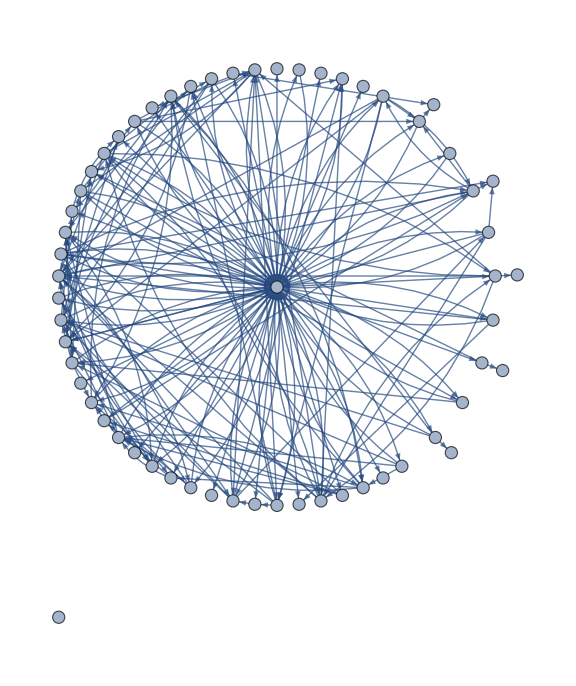

```mathematica
subG=Subgraph[simpleGraph,Keys@inDegree15OrMore,VertexLabels->Placed["Name",Tooltip],GraphLayout->"BalloonEmbedding",ImageSize->Large]
```

#### End of Graph

```mathematica
highlightedSubgraph=HighlightGraph[subG,{VertexList[subG],Property["elonmusk",VertexSize->5]},VertexSize->Thread[Drop[VertexList[subG],1]->2Rescale[Drop[DegreeCentrality[subG],1]]],ImageSize->Large]
```

-Graphics-

### Back to Musk Tweets

```mathematica
FileNames["*.mx"]
```

{cleanHashtags.mx,cleanLocations.mx,code.mx,locations.mx,mentionedUserData.mx,mentionedUserHashtags.mx,mentionedUserUserMentions.mx,muskTweets.mx,muskTweetsWithUserMentions.mx,mydata.tsv.mx,successMentionedUsersData.mx}

```mathematica
Get[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}]];
```

```mathematica
muskTweets
```

```mathematica
teslaTweets=muskTweets[Select[StringContainsQ[#Text,"Tesla"|"tesla"]&],All]
```

```mathematica
teslaTweets[DateHistogram[#,"Month"]&,"Date"]
```

```mathematica
muskTweets[DateHistogram[#,"Month"]&,"Date"]
```

```mathematica
(*tweetsJuly=muskTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 7, 1}],DateObject[{2020,7,31}]}],#Date]&],All];*)
```

```mathematica
(*tweetsApril=muskTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 4, 1}],DateObject[{2020,4,30}]}],#Date]&],All];*)
```

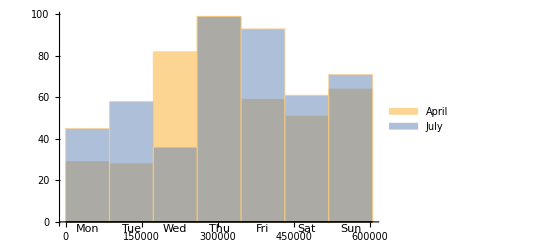

```mathematica
(*DateHistogram[{tweetsApril[All,"Date"],tweetsJuly[All,"Date"]},"Day",DateReduction->"Week",LabelingFunction->Tooltip,ChartLegends->{"April","July"}]*)
```

```mathematica
(*teslaTweetsJuly=teslaTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 7, 1}],DateObject[{2020,7,31}]}],#Date]&],All];*)
```

```mathematica
(*teslaTweetsApril=teslaTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 4, 1}],DateObject[{2020,4,30}]}],#Date]&],All];*)
```

```mathematica
(*DateHistogram[{
Complement[tweetsApril[All,"Date"],teslaTweetsApril[All,"Date"]],
teslaTweetsApril[All,"Date"],
Complement[tweetsJuly[All,"Date"],teslaTweetsJuly[All,"Date"]],
teslaTweetsJuly[All,"Date"]
},
"Day",DateReduction->"Week",
LabelingFunction->Tooltip,
ChartLayout->"Stacked",
ChartLegends->{"Others April","Tesla April","Others July","Tesla July"}]*)
```

```mathematica
days=DateDifference@@Normal[muskTweets[{-1,1},"Date"]]
```

```mathematica
num=muskTweets//Length
```

```mathematica
num/days
```

```mathematica
muskTweets[DateHistogram[#,"Day",DateReduction->"Month"]&,"Date"]
```

```mathematica
muskTweets[DateHistogram[#,"Hour",DateReduction->"Day"]&,"Date"]
```

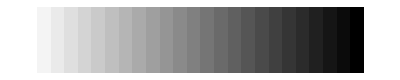

```mathematica
ArrayPlot[{Range[24]}]
```

```mathematica
ArrayPlot[Table[i+j,{i,7},{j,24}]]
```

```mathematica
weeklyBuzz[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},
dayOfWeekCounts=KeyTake[(KeySort[GroupBy[#1,First->Rest]]&)/@GroupBy[({DateObject[#1⟦1⟧]["DayName"],DateObject[#1⟦1⟧]["Hour"],#1⟦2⟧,#1⟦3⟧}&)/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=(Merge[{Length/@#1,Total/@#1},Flatten]&)/@dayOfWeekCounts;
(AssociateTo[dayOfWeekCountsSummary[#1],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#1]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets = ArrayPlot[ Map[#1⟦n⟧&,(Values[KeySort[dayOfWeekCountsSummary[#1]]]&)/@daysOfWeek,{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{MapIndexed[{#2⟦1⟧,#1}&,daysOfWeek],None},{Range[24],None}},
ImageSize->Full,
PlotLabel->"elonmusk Tweets"<>
Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"DateShort"}]<>" to"<>DateString[tweetsData[Max,"Date"],{"DateShort"}]<>")",
PlotLegends->Placed[Automatic,Below]]]
```

```mathematica
lastWeekEnd=DatePlus[DateObject[Today,"Second"],{-1,Monday}]
```

```mathematica
lastWeekBegin=DatePlus[lastWeekEnd,{-1,"Week"}]
```

```mathematica
tweetsLastWeek=muskTweets[Select[#Date≥lastWeekBegin&&#Date<lastWeekEnd&],All]
```

```mathematica
weeklyBuzz[tweetsLastWeek]
```

```mathematica
weeklyBuzz[tweetsLastWeek,2]
```

```mathematica
weeklyBuzz[tweetsLastWeek,3]
```

```mathematica
ReverseSortBy[muskTweets,#["RetweetCount"]&]
```

```mathematica
retweetCountOutlierThreshold=40000;
```

```mathematica
trainTweets=muskTweets[Select[#Date<DateObject["Nov 2020","Second"]&&#RetweetCount<=retweetCountOutlierThreshold&],All];
```

```mathematica
testTweets=muskTweets[Select[#Date≥ DateObject["Nov 2020","Second"]&&#Date<Today&&#RetweetCount<retweetCountOutlierThreshold&],All];
```

```mathematica
Length/@{trainTweets,testTweets}
```

```mathematica
p=Predict[Thread[{Normal@trainTweets[All,"Date"],Normal@trainTweets[All,"Text",cleanText]}]->Normal@trainTweets[All,"RetweetCount"],FeatureExtractor->{1->"NumericVector",2-> "TFIDF"}]
```

PredictorFunction[…]

```mathematica
Export[FileNameJoin[{Directory[],"predictor.wmlf"}],p]
```

```mathematica
p=Import[FileNameJoin[{Directory[],"predictor.wmlf"}]]
```

```mathematica
pm=PredictorMeasurements[p,Thread[Thread[{Normal[testTweets[All,"Date"]],Normal[testTweets[All,"Text",cleanText]]}]->Normal[testTweets[All,"RetweetCount"]]]];
pm["ComparisonPlot"]
```

```mathematica
retweetCandidates=testTweets[Select[#RetweetCount≤500&&Round@p[{#Date,cleanText[#Text]}]≥2000&],<|"ActualRetweets"->#RetweetCount,
"PredictedRetweets"->Round@p[{#Date,cleanText[#Text]}],
"Hashtags"->#Hashtags,
"Text"->#Text,"Date"->#Date,"URL"->#URL|>&]
```

#### FeatureSpacePlot and CLusters

```mathematica
(*rankedMentions=muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"]*)
```

```mathematica
(*KeySelect[muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"],StringMatchQ[#,___~~"Tesla"~~___,IgnoreCase->True]&]*)
```

```mathematica
(*daysBegin = DateObject["Dec 2020","Second"];
daysEnd = DatePlus[daysBegin,{1,"Month"}];
(*daysBegin+Quantity[1,"Month"]*)
decTweets = muskTweets[Select[#Date≥daysBegin && #Date ≤daysEnd &],All]*)
```

```mathematica
(*FeatureSpacePlot[decTweets[All,"Usermentions"]]*)
```

```mathematica
(*FeatureSpacePlot[decTweets[StringSplit/*Flatten/*DeleteDuplicates,"Text",cleanText],
FeatureExtractor->NetModel["GloVe 50-Dimensional Word Vectors Trained on Tweets"]]*)
```

```mathematica
(*wordVectors = FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"];*)
```

```mathematica
(*tweetWordCentroids = DeleteCases[Thread[Total/@FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"]->Normal[decTweets[All,"Text",cleanText]]],0->___];*)
```

#### Segue

```mathematica
tweetWordCentroids[[184]]
```

0→

```mathematica
decTweets[[184]]["Text"]
```

100

```mathematica
FullForm@%
```

"100"

```mathematica
Select[Keys[tweetWordCentroids],Length[#]≠50&]
```

{0}

```mathematica
Position[Keys[tweetWordCentroids],0]
```

{{184}}

```mathematica
Manipulate[Part[tweetWordCentroids,n],{n,1,Length[tweetWordCentroids],1}]
```

Part::partd: Part specification tweetWordCentroids⟦184⟧ is longer than depth of object.

```mathematica
Length[tweetWordCentroids]
```

205

```mathematica
DeleteCases[tweetWordCentroids,{0->_}]
```

{1}
 |  |  |  |

```mathematica
Length@%
```

205

#### End Segue

```mathematica
(*features2D=Thread[DimensionReduce[Keys[tweetWordCentroids],2]->Values[tweetWordCentroids]];*)
```

```mathematica
(*First@features2D*)
```

```mathematica
(*ListPlot[MapThread[Tooltip[#1,#2]&,{Keys@features2D,Values@features2D}]]*)
```

```mathematica
(*clusters=FindClusters[features2D[[All,1]]];*)
```

```mathematica
(*ListPlot[clusters,PlotLegends->Table["Cluster "<>ToString[i],{i,Length[clusters]}]]*)
```

```mathematica
(*Length/@FindClusters[features2D]*)
```

```mathematica
(*Mean[{20,159,5,6,10,4}]*)
```

34

### December tweet Analysis

```mathematica
decTweets = muskTweets[Select[#Date≥daysBegin && #Date ≤daysEnd &],All]
```

```mathematica
clusters=FindClusters[Thread[Total/@FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"]->Normal[decTweets[All,"Text",cleanText]]],3,Method-> "Agglomerate"];
```

```mathematica
WordCloud/@(Flatten[StringSplit[#]]&/@clusters)
```

```mathematica
labels=Classify["Sentiment",decTweets[All,"Text"]]
```

```mathematica
PieChart[Counts[Classify["Sentiment",decTweets[All,"Text"]]],ChartLabels->Placed[Automatic,"RadialCallout"]]
```

```mathematica
Cases[({#1->Classify["Sentiment",cleanText[#1]]}&)/@decTweets[All,"Text"],{_->"Negative"}]
```

```mathematica
(*teslaTweets=muskTweets[Select[StringContainsQ[#Text,"Tesla"]&],"Text"]*)
```

```mathematica
(*Length[teslaTweets]*)
```

492

```mathematica
(*nonTesla=RandomSample[muskTweets[Select[!StringMatchQ[#Text,__~~"data"~~__,IgnoreCase->True]&],"Text"],2 Length[teslaTweets]]*)
```

```mathematica
(*teslaClassifier = Classify[<|"Tesla"->Normal[teslaTweets],"NonTesla"->Normal[nonTesla]|>,Method->"LogisticRegression"]*)
```

ClassifierFunction[…]

```mathematica
(*teslaLabels=<|"PredictedLabel"->teslaClassifier[cleanText[#["Text"]]],"Usermentions"->#["Usermentions"],"Text"->#["Text"]|>&/@Normal@decTweets[All,{"Usermentions","Text"}];*)
```

```mathematica
(*PieChart[Counts[#["PredictedLabel"]&/@teslaLabels],ChartLabels->Automatic]*)
```

```mathematica
(*Dataset[teslaLabels][GroupBy[#PredictedLabel&]]*)
```

#### More Graphs

```mathematica
Get[FileNameJoin[{Directory[],"MentionedUserUserMentions.mx"}]]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1216,oyvi00i→{NyrAutomobile,grandayy,NyrAutomobile,grandayy,grandayy,Vebteo,Vebteo,6,NEWSLEAKSGTAS,Fact,imermot,TailosiveNet,StianTStaysman,tyler420699,TGdog}}
 |  |  |  |

```mathematica
edges=Select[mentionedUserUserMentions,!SameQ[#[[2]],Null]&]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1216,oyvi00i→{NyrAutomobile,grandayy,NyrAutomobile,grandayy,grandayy,Vebteo,Vebteo,6,NEWSLEAKSGTAS,Fact,imermot,TailosiveNet,StianTStaysman,tyler420699,TGdog}}
 |  |  |  |

```mathematica
AppendTo[edges,"elonmusk"->Keys[mentionedUserUserMentions]]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1217,elonmusk→{elonmusk,jack,flcnhvy,smvllstvrs,ErcXspace,Erdayastronaut,1206,newscientist,Foxfire40900590,JakeTheHuman28,j_brorsson,Bryr32,oyvi00i}}
 |  |  |  |

```mathematica
g=Flatten[Thread[#[[1]]->DeleteDuplicates[#[[2]]]]&/@edges];
```

```mathematica
sg=SimpleGraph[g]
```

```mathematica
inDegrees=SortBy[#->VertexInDegree[sg,#]&/@VertexList[sg],Last];
```

```mathematica
inDegree3OrMore=ReverseSort[Select[Association[inDegrees],#>2&]];
```

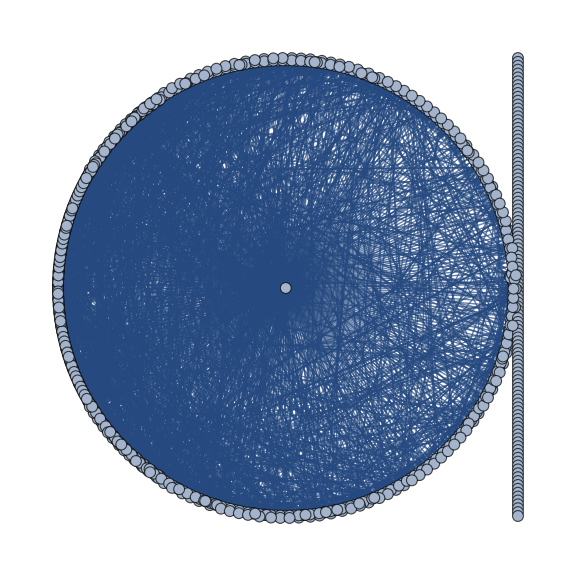

```mathematica
subG=Subgraph[sg,Keys@inDegree3OrMore,VertexLabels->Placed["Name",Tooltip],GraphLayout->"BalloonEmbedding",ImageSize->Large]
```

```mathematica
highlightedSubgraph=HighlightGraph[subG,{VertexList[subG],Property["WolframResearch",VertexSize->12]},VertexSize->Thread[Drop[VertexList[subG],1]->10 Rescale[Drop[DegreeCentrality[subG],1]]],ImageSize->Medium]
```

-Graphics-

```mathematica
comms=FindGraphCommunities[subG];
```

#### End of Graph

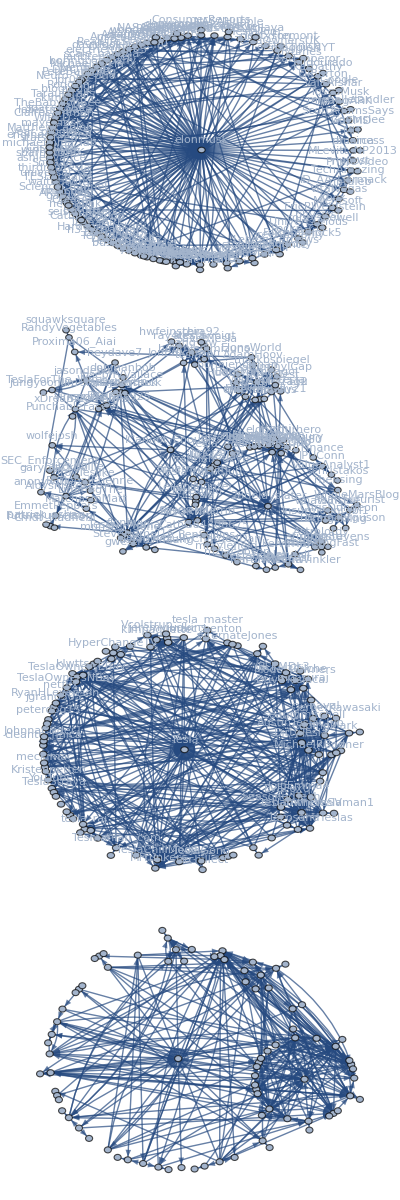

```mathematica
Column[Subgraph[subG,#,VertexLabels->Placed["Name",Above]]&/@FindGraphCommunities[subG][[1;;4]]]
```

### Visuals

```mathematica
Get[FileNameJoin[{Directory[],"muskTweetsWithUsermentions.mx"}]];
```

```mathematica
decAndAfterTweets=muskTweets[Select[#Date≥DateObject["Dec 2020","Second"]&],All]
```

```mathematica
userMentionCloud=WordCloud[Normal[decAndAfterTweets[Flatten,"Usermentions"]]]
```

```mathematica
tweetTextCloud=decAndAfterTweets[Flatten/*StringSplit/*WordCloud,"Text",StringDelete[cleanText[#],"#"|"@"~~__]&]
```

```mathematica
cleanText[txt_String]:=StringTrim[StringReplace[DeleteStopwords[StringDelete[txt,{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"RT","RN","JK","w/","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,s_/;!PrintableASCIIQ[s]}]],Repeated[WhitespaceCharacter]->" "]]
removeHTML[s_String]:=StringTrim[StringReplace[StringReplace[StringDelete[s,{"&amp","&gt","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,c_/;!PrintableASCIIQ[c]}],Except[{"@","#","_"},PunctuationCharacter]->" "],Repeated[WhitespaceCharacter]->" "]]
```

```mathematica
hashtagCloud=WordCloud[Normal[decAndAfterTweets[Flatten,"Hashtags"]]]
```

```mathematica
Grid[{{Labeled[Show[hashtagCloud,ImageSize->Scaled[0.9]],Style["Hashtags",Bold,"Text",Gray],Top],Labeled[Show[tweetTextCloud,ImageSize->Scaled[0.9]],Style["Text Content",Bold,"Text",Gray],Top]},{Labeled[Show[userMentionCloud,ImageSize->Scaled[0.9]],Style["User Mentions",Bold,"Text",Gray],Top],SpanFromAbove}},Dividers->Center,FrameStyle->Black,Alignment->{Top,Center},Frame->All,ItemSize->{{Scaled[.5],Scaled[.5]}}]
```

```mathematica
weeklyBuzz[decAndAfterTweets,1]
```

```mathematica
weeklyTweets=weeklyBuzz[decAndAfterTweets,1];
weeklyRetweets=weeklyBuzz[decAndAfterTweets,2];
weeklyLikes=weeklyBuzz[decAndAfterTweets,3];
```

```mathematica
TabView[{"Tweets"->weeklyTweets,"Retweets"->weeklyRetweets,"Likes"->weeklyLikes},ControlPlacement->Bottom]
```

```mathematica
weeklyBuzzColor[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},dayOfWeekCounts=KeyTake[KeySort[GroupBy[#,First->Rest]]&/@GroupBy[{DateObject[#[[1]]]["DayName"],DateObject[#[[1]]]["Hour"],#[[2]],#[[3]]}&/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=Merge[{Length/@#,Total/@#},Flatten]&/@dayOfWeekCounts;(AssociateTo[dayOfWeekCountsSummary[#],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets=ArrayPlot[Map[#[[n]]&,((Values[KeySort[dayOfWeekCountsSummary[#]]]&)/@daysOfWeek),{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{Table[{i,daysOfWeek[[i]]},{i,7}],None},{Range[24],None}},ImageSize->Full,PlotLabel->"elonmusk Tweets"<>Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"MonthNameShort"," ","Day"}]<>" to "<>DateString[tweetsData[Max,"Date"],{"Day",", ","Year"}]<>")",PlotLegends->Placed[Automatic,Below],PlotTheme->"Marketing"]]
```

```mathematica
weeklyTweetsColor=weeklyBuzzColor[decAndAfterTweets,1];
weeklyRetweetsColor=weeklyBuzzColor[decAndAfterTweets,2];
weeklyLikesColor=weeklyBuzzColor[decAndAfterTweets,3];
```

```mathematica
TabView[{"Tweets"->weeklyTweetsColor,"Retweets"->weeklyRetweetsColor,"Likes"->weeklyLikesColor},ControlPlacement->Bottom]
```

### Deployment on the Cloud

```mathematica
(cleanText[txt_String]:=StringTrim[StringReplace[DeleteStopwords[StringDelete[txt,{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"RT","RN","JK","w/","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,s_/;!PrintableASCIIQ[s]}]],Repeated[WhitespaceCharacter]->" "]];
weeklyBuzzColor[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},dayOfWeekCounts=KeyTake[KeySort[GroupBy[#,First->Rest]]&/@GroupBy[{DateObject[#[[1]]]["DayName"],DateObject[#[[1]]]["Hour"],#[[2]],#[[3]]}&/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=Merge[{Length/@#,Total/@#},Flatten]&/@dayOfWeekCounts;(AssociateTo[dayOfWeekCountsSummary[#],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets=ArrayPlot[Map[#[[n]]&,((Values[KeySort[dayOfWeekCountsSummary[#]]]&)/@daysOfWeek),{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{Table[{i,daysOfWeek[[i]]},{i,7}],None},{Range[24],None}},ImageSize->Full,PlotLabel->"elonmusk Tweets"<>Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"MonthNameShort"," ","Day"}]<>" to "<>DateString[tweetsData[Max,"Date"],{"Day",", ","Year"}]<>")",PlotLegends->Placed[Automatic,Below],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],ColorFunctionScaling->True]];
panel[handle_String]:=Module[{begin,end,twitter,tweets,hashtagCloud,weeklyBuzz,tweetSentiments,favouriteCount,retweetCount},begin=DateObject[PreviousDate["Week"],TimeObject[{00}]];
end=DatePlus[begin,{1,"Week"}];
twitter=ServiceConnect["Twitter"];
tweets=twitter["TweetList","Username"->handle,"Elements"->"FullData",MaxItems->500][Select[#Date≥begin&&#Date≤end&],All];
hashtagCloud=WordCloud[Normal[tweets[Flatten,"Hashtags"]]];
weeklyBuzz=weeklyBuzzColor[tweets,1];
tweetSentiments=PieChart[Merge[{<|"Negative"->0,"Neutral"->0,"Positive"->0|>,Counts[Classify["Sentiment"][tweets[All,#Text&]]]},Total],PlotTheme->{"Web","Square"},ChartStyle->{RGBColor[0.8115292,0.2810584,0.1],GrayLevel[0.5],RGBColor[0.,0.4,0.]},ChartLegends->Placed[{"Negative","Neutral","Positive"},Below],PlotLabel->"Tweet Sentiment Analysis",ImageSize->Small];
favouriteCount=Histogram[Normal[tweets[All,"FavoriteCount"]],{1},"Count",PlotTheme->{"Web","Square"},PlotLabel->"Favorite Count",FrameLabel->{{"Number of Tweets",None},{"Number of Likes",None}},Frame->{{True,False},{True,False}},ImageSize->Small];
retweetCount=Histogram[Normal[tweets[All,"RetweetCount"]],{1},"Count",PlotTheme->{"Web","Square"},PlotLabel->"Retweet Count",FrameLabel->{{"Number of Tweets",None},{"Number of Retweets",None}},Frame->{{True,False},{True,False}},ImageSize->Small];
Rasterize@Panel[Grid[{{weeklyBuzz,SpanFromLeft,Column[{" ",Show[hashtagCloud,ImageSize->Scaled[0.95]]," ",Style["Hashtags","Text",14,Gray]},Alignment->Center]},{Show[favouriteCount,ImageSize->Scaled[0.9]],Show[retweetCount,ImageSize->Scaled[0.9]],Show[tweetSentiments,ImageSize->Scaled[0.9]]}},ItemSize->{{Scaled[0.3],Scaled[0.3],Scaled[0.3]}}],Style[handle~~" Tweets at a Glance","Subsubtitle"],Bottom]];
panel[#handle]&)
```

panel[#handle]&

```mathematica
panel[#handle]&
```

```mathematica
CloudDeploy[FormPage[{"handle","Twitter Handle"}->"String",panel[Slot["handle"]]&,AppearanceRules-><|"Title"->"Tweets Last Week","Description"->"Weekly report on tweets from a particular account"|>],"TwitterCloud"]
```